# Balanced Photo Detector Analysis: Vetting Process

## Initialization of Directory and Functions

## Directory Setting and Folder Selection

```mathematica
dropBoxOn=FileNameJoin[{"Dropbox","00School","research","DataRuns"}];
If[SystemInformation["Kernel","OperatingSystem"]=="Unix",
folder=FileNameJoin[{"/","home","karl",dropBoxOn}]; ,(* Home coputer is Linux, so needs "/" at beginning *)
folder=FileNameJoin[{"C:","Users","kahrendsen2",dropBoxOn}];(* Lab computer is Windows, so needs "C:" at beginning"*)
];
SetDirectory[folder];

FileNames[]
```

{15-06-09_USBCounterError,15-07-06mockPolarizationData,16-01-14,16-01-21_Data,16-05-25_PolarizationData,16-07-06_PolarizationData,16-08-04_PolarizationData,16-08-07_HeliumTargetPictures,16-08-09_PolarizationData,16-10-17_polarimeter,16-10-27_DataReport,16-11-03_faradayRotation,16-11-07_faradayRotation,16-11-18_faradayRotation,16-12-09_faradayRotation,17-01-31,17-02-17_plusMinus,17-03-06_PlusMinusWavemeter,17-03-10_non-RbFaradayRotation,17-03-15_AimingFor5e12,17-03-15_wavemeterNoRb,17-03-28,17-03-29_pumpLaserFindingCircular,17-03-30_WavemeterReliability,17-04-04_polarization,17-04-06_polarization,17-04-07_wmReliability,17-04-18,17-04-18_polarization,17-04-22,17-04-25_ProbePolarizationDriftOpenChamber,17-04-30_laserReport,17-05-17_DirtyGunRun,17-05-18_ProbeDrift,17-05-19_BetterLaser,17-05-24_SimplifiedPolarization,17-05-25_LaserProfiling,17-05-25_LaserProfiling - Shortcut.lnk,17-06-02,17-06-06_IntensityOfProbeStudy,17-06-11,17-06-13,17-06-16,17-06-17,17-06-25,17-07-01_nRbVsBufferGasAnalysis,17-07-01_PumpLaserAnalysis,17-07-03_lowerNRb_BGPStudy,17-07-03_ProbeDrift,17-07-03_pumpBroadening,17-07-06_lotsOfProbeMeasurements,17-07-06_MagneticField,17-07-06_probePower,17-07-12_polVsPumpPower,17-08-01_rgaInitialScans,17-08-03_redoingSystemDiagnostic,17-08-06_probeDrift,17-08-18_furtherPolarizationStudy,17-08-19_furtherPolarizationStudy2,17-08-22_furtherPolarizationStudyFoundLeak,17-08-29_BvsProbePower_probeDetuneVsMagnetRot,17-09-05_Polarizations_100mTBGP,17-09-20,17-10-03_ElectronGun,17-10-16_ElectronGun,17-10-24_UnpolarizedPolarization,17-10-26_24And30eVRuns,17-10-28_24and30eVRedux,17-11-04_MoreUnpolarizedRuns,17-11-06_UnpolarizedRuns2,17-11-15_BalancedPhotoDetector,17-11-18_SystemDiagnosis,17-12-18_SystemDiagnosis,17-12-20_PolarizingElectrons,18-01-03_PolarizingElectrons,18-01-04_PolarizingElectrons,18-01-10_ChamberWarming,18-01-11_SystemDiagnostics,18-01-12_recreatingPolFigure,18-01-13_recreatingPolFigureIncreasedT,18-01-16_morePolarization,18-01-20_electronPolarization,18-01-25_excitationFunctions,18-01-28_bufferGasPressureVsCounts,18-01-28_hayesReproduction,18-02-12_polarizedElectrons,18-02-13,18-02-24_DataFrom18-02-13AllElectronEi100,18-02-27,18-03-01,18-03-02,18-03-03,18-03-06_RubidiumOnWalls,18-03-18_100mTorrBGP,18-03-22_Ei=37eV,18-03-23_pumpScan,18-03-25_springBreakDataReview,18-03-27_770mTorr,18-03-28_PumpPowerScan,18-04-18,18-05-04,18-05-07,18-06-03,2018-04-09_PumpLaserRazorProfile,2018-06-07,2018-06-15_BalancedPhotoDetector,2018-06-19_CO2_Data,2018-06-21_ProbeWalkData,2018-06-25_RbProfiles,2018-06-26_SpectrumAnalyzer,2018-06-29_ElectronPolarizationData,2018-07-06_ReorganizingNrbStuff,2018-07-10_BalancedPhotoDetectorRound2,2018-07-10_newAoutToVoltageConversionForHeTarget,2018-07-19_probeLaserProfiling,2018-07-20_taPROReceivingData,2018-07-24_findingNewPumpQWP,2018-07-24_roughingPumpForelineTrapBakeout,2018-07-31_excitationFunctionStudy,2018-08-04_BGPTestPressureAndTempTracking,2018-08-06_excitationFunctionStudyRbCompare,2018-08-11_firstNewLaserElectronPolarization,BalancedPhotodetectorRun1and2Data.zip,dataDump,driveCurrentsAndPowersAndWavelengths.xlsx,pumpQWP,README.txt,reallyNiceData,temp,wavemeterOffsets,~$driveCurrentsAndPowersAndWavelengths.xlsx}

```mathematica
SetDirectory[FileNameJoin[{folder,"2018-07-10_BalancedPhotoDetectorRound2","data","magnetsOnLongTimeData"}]];
absFiles=FileNames[StringExpression["RbAbs",__,"_",__,DigitCharacter,".dat"]]
rotationFiles=FileNames["FDayRotation"~~RegularExpression[".{17,17}"]~~".dat"]
```

{RbAbs2018-07-16_200535.dat}

{FDayRotation2018-07-16_202950.dat,FDayRotation2018-07-16_203052.dat}

## Important Constants

```mathematica
(*Physical constants *)
c=2.99792458*^10; (* cm/s *)
re=2.8179*^-13; (* cm *)
cellLength=2.794;(* cm *)
fge=0.34231; (* dimensionless *)
k=4/3; (* dimensionless *)
BdotL; (* G*cm *)
μ=9.2740*^-21; (* g*cm^2*s^-2*G^-1 *)
h=6.6261*^-27; (* g*cm^2*s^-1 *)
ν0=377107.463*^9;  (* s^-1 *)
λ0=c/ν0; (* cm *)
gHzToHz=1*^9;

(* Note that Q is a constant that consists of variables that are always the same between equations. 
It does not include factors of c, 2π, ν or λ  Q=(Subscript[r, e] Subscript[f, ge] κ Subscript[μ, B])/h which has dimensions of [ L^1 T^-1 G^-1 ]*)
Q=(re fge k μ)/h;
nDensModel:=a0+(a2(δ+ν0)^2)/δ^2+(a4(δ+ν0)^2)/δ^4;
nDensC=(4 π ν0^2)/(c  Q);
```

## General File Manipulation

```mathematica
GenerateListOfFileNames[prefix_,date_,runtimes_]:=Module[{j,fileNames},
fileNames={};
For[j=1,j≤Length[runtimes],j++,
AppendTo[fileNames,StringJoin[prefix,date,"_",ToString[runtimes[[j]]],".dat"]]
];
fileNames
];

(* If given a list of files*)
GetIndexOfFilenameFromTimestamp[files_,timestamp_]:=Module[{i,index},
For[i=1,i≤Length[files],i++,
If[StringContainsQ[ files[[i]],timestamp],index=i]
];
index
];


GetFileHeaderInfo[dataFileName_]:=Module[{rawFile,data,association,k,rawImport,removedNulls,joinedWithSpaces},
rawFile=Import[dataFileName];
data={};
association=Association[];
k=1;
While[StringPart[rawFile[[k]][[1]],1]=="#",
If[Length[rawFile[[k]]]> 2,
rawImport=Take[rawFile[[k]],{2,-1}];
removedNulls=DeleteCases[rawImport,Null];
joinedWithSpaces=StringRiffle[removedNulls];
association=Append[association,StringReplace[rawFile[[k]][[1]],{"#"-> "",":"->""}]->joinedWithSpaces];
,
association=Append[association,StringReplace[rawFile[[k]][[1]],{"#"->"",":"->""}]->rawFile[[k]][[2]]];
];
k++;
];
association
];

GetFileDataset[dataFileName_]:=Module[{rawFile,headerStrippedData,columnHeaderLineNumber,lastColumnToImport,j,k,ass,tabularData,ds,rbAbsorptionRef,rbAbsorptionPro},
rawFile=Import[dataFileName];
k=1;

While[StringPart[rawFile[[k]][[1]],1]=="#",
k++;
];
headerStrippedData=Take[rawFile,{k,-1},All];
tabularData={};
For[j=2,j≤Length[headerStrippedData],j++,
If[Length[headerStrippedData[[j]]]>1,
ass=Association[];
For[k=1,k≤Length[headerStrippedData[[j]]],k++,
ass=Append[ass,headerStrippedData[[1]][[k]]->headerStrippedData[[j]][[k]]];
];
tabularData=Append[tabularData,ass];
]
];
ds =Dataset[tabularData]
];
ImportFile[dataFileName_]:={GetFileHeaderInfo[dataFileName],GetFileDataset[dataFileName]}
SetAttributes[GetFileDataset,Listable];
SetAttributes[GetFileHeaderInfo,Listable];
SetAttributes[ImportFile,Listable];
```

## Electron Polarization Functions

```mathematica
colorBlindPallete={RGBColor[230/255,159/255,0],RGBColor[86/255,180/255,233/255],RGBColor[0/255,158/255,115/255],RGBColor[240/255,228/255,66/255],RGBColor[0/255,114/255,178/255],RGBColor[213/255,94/255,0/255],RGBColor[204/255,121/255,167/255],RGBColor[0/255,0/255,0/255]};
SetOptions[Plot,BaseStyle->{FontSize->24},Frame->True,LabelStyle->27,GridLines->Automatic];
SetOptions[ListPlot,BaseStyle->{FontSize->24},Frame-> True,LabelStyle->27,ImageSize->{960,600},GridLines->Automatic];
SetOptions[ListLogPlot,BaseStyle->{FontSize->24},ImageSize->Large,LabelStyle->27,ImageSize->{960,600},GridLines->Automatic];
SetOptions[BarChart,BaseStyle->{FontSize->18,PointSize[Large]},ImageSize->Large,GridLines->Automatic];
stokesNames={"p0","p1","p2","p3_mag","p3_c2","p3_s2"};
stokesErrNames={"p0err","p1err","p2err","p3_magerr","p3_c2err","p3_s2err"};
nA=1*^-9;
mTorr=1*^-3;
alpha=20.4*π/180;
beta=68.7*π/180;
deltaAB=alpha-beta;
delta=94.54*π/180 (*Munir's reported 1.66 plus or minus .01*);

(*Physical constants *)
c=2.99792458*^10; (* cm/s *)
re=2.8179*^-13; (* cm *)
cellLength=2.794;(* cm *)
fge=0.34231; (* dimensionless *)
k=4/3; (* dimensionless *)
BdotL; (* G*cm *)
μ=9.2740*^-21; (* g*cm^2*s^-2*G^-1 *)
h=6.6261*^-27; (* g*cm^2*s^-1 *)
ν0=377107.463*^9;  (* s^-1 *)
λ0=c/ν0; (* cm *)
gHzToHz=1*^9;
Q=(re fge k μ)/h;
nDensC=2*h/(c*re*fge*k*μ)*10^18; (* cm^2*g*s^-1  *  G^-1*cm^-1  *  cm^-1*s  *  cm^-1  *  g^-1*cm^-2*s^2*G  *)
(*Conversion Factor. is in 1/(Hz)^2, so we need *10^18 to convert to 1/(GHz)^2*)


alphaOld=3.2*π/180;
betaOld=-6.95*π/180;
rev=1;

Needs["ErrorBarPlots`"]

FourierFit[list_,rev_]:=Module[{fit,function,dataPts,stepSize,dataPtsPerRev,angles,data(*,C0,C2,C4,S2,S4*)},

function[θ_]= C0+C2 Cos[2(θ+θo)]+C4 Cos[4(θ+θo)]+S2 Sin[2(θ+θo)]+S4 Sin[4(θ+θo)];
dataPts=Length[list];
dataPtsPerRev=dataPts/rev;
angles=Range[0,(2π*rev)-2π/dataPtsPerRev,2π/dataPtsPerRev];
data=Transpose[{list,angles}];
fit=NonlinearModelFit[data,function[θ],{{C0,1000},C2,C4,S2,S4,θo},θ]
];


DFT[list_,rev_:1]:=Module[{numItems,i,k,j,reconstructionCos,reconstructionSin,returnCos,errorsCos,returnSin,errorsSin,intensity},
returnCos={};
errorsCos={};
returnSin={};
errorsSin={};
reconstructionCos={};
reconstructionSin={};
numItems=Length[list];

For[j=0,j<numItems/2,j++,
AppendTo[returnCos,0];
AppendTo[returnSin,0];

];

For[i=1,i<=numItems,i++,
intensity=list[[i]];
For [k=0,k<numItems/2,k++,
If[k==0 ||k==(numItems/2-1),
returnCos[[k+1]]=N[returnCos[[k+1]]+1/numItems*intensity*Cos[2*π *k *rev* (i-1)/numItems]];
returnSin[[k+1]]=N[returnSin[[k+1]]+1/numItems*intensity*Sin[2*π *k *rev* (i-1)/numItems]];,
returnCos[[k+1]]=N[returnCos[[k+1]]+2/numItems*intensity*Cos[2*π *k* rev *(i-1)/numItems]];
returnSin[[k+1]]=N[returnSin[[k+1]]+2/numItems*intensity*Sin[2*π *k* rev *(i-1)/numItems]];
];
];
];
(*

For[j=0,j<numItems/2,j++,
AppendTo[errorsSin,0];
AppendTo[errorsCos,0];
For[i=1,i<=numItems,i++,
intensity=list[[i]];
AppendTo[reconstructionCos,0];
AppendTo[reconstructionSin,0];
reconstructionCos[[i]]=intensity/Cos[2*π*j*rev*(i)/numItems] ;
If[j==0,reconstructionSin[[i]]=0,reconstructionSin[[i]]=intensity/Sin[2*π*1.0001*j*rev*(i)/numItems];];
For [k=0,k<numItems/2,k++,
If[k≠j,
reconstructionCos[[i]]-=(returnCos[[k+1]]*Cos[2*π*k*rev*(i)/numItems] +returnSin[[k+1]]*Sin[2*π*k*rev*(i)/numItems] )/Cos[2*π*j*rev*(i)/numItems];
If[j==0,reconstructionSin[[i]]=0,reconstructionSin[[i]]-=(returnCos[[k+1]]*Cos[2*π*k*rev*(i)/numItems] +returnSin[[k+1]]*Sin[2*π*k*rev*(1)/numItems] )/Sin[2*π*1.0001*j*rev*(i)/numItems]];
];
];
errorsSin[[j+1]]+=Power[reconstructionSin[[i]]-returnSin[[j+1]],2];
errorsCos[[j+1]]+=Power[reconstructionCos[[i]]-returnCos[[j+1]],2];
];
errorsSin[[j+1]]=Sqrt[errorsSin[[j+1]]/numItems];
errorsCos[[j+1]]=Sqrt[errorsCos[[j+1]]/numItems];
];
*)
{{returnSin,errorsSin},{returnCos,errorsCos}}
];
StokesParametersFromFourierCoefficients[fc_(*Fourrier Coefficients*),rev_:rev,alpha_:alpha,beta0_:beta,delta_:delta]:=Module[{c0,c2,c4,s2,s4,stokes},
stokes={0,0,0,0,0,0};
c0=fc[[2]][[1]][[1]];
c2=fc[[2]][[1]][[3]];
c4=fc[[2]][[1]][[5]];
s2=fc[[1]][[1]][[3]];
s4=fc[[1]][[1]][[5]];
stokes[[1]]=c0-(1+Cos[delta])/(1-Cos[delta])*(c4*Cos[4 alpha+4 beta0]+s4*Sin[4 alpha+4 beta0]);
stokes[[2]]=2/(1-Cos[delta])*(c4*Cos[2alpha + 4 beta0]+s4*Sin[2alpha + 4 beta0])/stokes[[1]];
stokes[[3]]=2/(1-Cos[delta])*(s4*Cos[2alpha + 4 beta0]-c4*Sin[2alpha + 4 beta0])/stokes[[1]];
stokes[[4]]=Sqrt[c2^2+s2^2]/(Sin[delta]^2 stokes[[1]]);
stokes[[5]]=c2/(Sin[delta]Sin[2 alpha + 2 beta0]stokes[[1]]);
stokes[[6]]=-s2/(Sin[delta]Cos[2 alpha + 2beta0]stokes[[1]]);
stokes];

(* 
Someday when I'm bored, I can try to implement the asoociation version of the stokes vectors. Today is not that day
StokesParametersFromFourierCoefficients[fc_(*Fourrier Coefficients*),rev_:rev,alpha_:alpha,beta0_:beta,delta_:delta]:=Module[{c0,c2,c4,s2,s4,stokes},
stokes=<||>;
c0=fc[[2]][[1]][[1]];
c2=fc[[2]][[1]][[3]];
c4=fc[[2]][[1]][[5]];
s2=fc[[1]][[1]][[3]];
s4=fc[[1]][[1]][[5]];
AppendTo[stokes,stokesNames[[1]]->c0-(1+Cos[delta])/(1-Cos[delta])*(c4*Cos[4 alpha+4 beta0]+s4*Sin[4 alpha+4 beta0])];
AppendTo[stokes,stokesNames[[2]]->2/(1-Cos[delta])*(c4*Cos[2alpha + 4 beta0]+s4*Sin[2alpha + 4 beta0])/stokes[[1]]];
AppendTo[stokes,stokesNames[[3]]->2/(1-Cos[delta])*(s4*Cos[2alpha + 4 beta0]-c4*Sin[2alpha + 4 beta0])/stokes[[1]]];
AppendTo[stokes,stokesNames[[4]]->Sqrt[c2^2+s2^2]/(Sin[delta]^2 stokes[[1]])];
AppendTo[stokes,stokesNames[[5]]->c2/(Sin[delta]Sin[2 alpha + 2 beta0]stokes[[1]])];
AppendTo[stokes,stokesNames[[6]]->-s2/(Sin[delta]Cos[2 alpha + 2beta0]stokes[[1]])];
stokes
];
*)

StokesParametersFromRawFourierData[intensityArray_,rev_:rev,alpha_:alpha,beta0_:beta,delta_:delta]:=
Module[{fc(*Fourrier Coefficients*),c0,c2,c4,s2,s4,stokes},
fc=DFT[intensityArray,rev];
StokesParametersFromFourierCoefficients[fc,rev,alpha,beta0,delta]
];

StokesParametersFromPolFile[polFile_,alpha_,beta0_,delta_,rev_]:=
Module[{intensityArray,f},
intensityArray=Normal[polFile[[2]][All,"COUNT"]];
StokesParametersFromRawFourierData[intensityArray,rev,alpha,beta0,delta]
];

StokesParametersFromPolFileName[polFileName_,alpha_,beta0_,delta_]:=
Module[{intensityArray,f,rev},
f=ImportFile[polFileName];
intensityArray=Normal[f[[2]][All,"COUNT"]];
rev=f[[1]]["REV"];
StokesParametersFromPolFile[f,alpha,beta0,delta,rev_]
];

GetLinearPolarizationFraction[fileName_]:=Module[{data,angle,intensityArray,angleRAD,fc,intensity,linearPolarization,linearPolarizationFraction},
data=GetFileDataset[fileName];
intensityArray=Transpose[data][[2]];
fc=DFT[intensityArray,1] (*fc=fourier coefficients*);
intensity=fc[[2]][[1]];
linearPolarization=Sqrt[(fc[[2]][[3]])^2+(fc[[1]][[3]])^2];
linearPolarizationFraction=linearPolarization/intensity
];
SetAttributes[GetLinearPolarizationFraction,Listable];
GetAngle[fileName_]:=Module[{data,intensityArray,angleRAD,fc,intensity,linearPolarization,linearPolarizationFraction},
data=GetFileDataset[fileName];
intensityArray=Transpose[data][[2]];
fc=DFT[intensityArray,1] (*fc=fourier coefficients*);
.5*ArcTan[fc[[1]][[3]],fc[[2]][[3]]]
];
SetAttributes[GetAngle,Listable];



GetAverageCountRateFromFileNames[fileNames_]:=Module[{files},
files=ImportFile[fileNames];
GetAverageCountRateFromFiles[files]
];

(* See Nate Clayburn's explanation on Background Subtraction p. 129 eq. 93*)
(* Returns a list of two items.
	the first item is a list of the intensity reaching the PMT at each step of the polarimeter.
	the second item is the standard deviation of these counts
*)
GetAverageCountRateFromFiles[files_]:=Module[{i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,j},
nDataPts=Length[Normal[files[[1]][[2]][All,"COUNT"]]];
sum={};errorSum={};
For[j=1,j≤ nDataPts,j++,
sum=AppendTo[sum,0];
errorSum=AppendTo[errorSum,0];
];
For[i=1,i≤Length[files],i++,
counts=Normal[files[[i]][[2]][All,"COUNT"]];
current=Normal[files[[i]][[2]][All,"CURRENT"]];
dwell=files[[i]][[1]]["DWELL(s)"];
nCycles=Length[files];
For[j=1,j≤nDataPts,j++,
sum[[j]]+=counts[[j]]/nCycles/dwell;
errorSum[[j]]+=counts[[j]]/(nCycles^2*dwell^2);
];
];
For[j=1,j≤ nDataPts,j++,
errorSum[[j]]=Sqrt[errorSum[[j]]];
];
{sum,errorSum}
];

GetCurrentNormalizedAverageCountRateFromFiles[files_]:=Module[{t,scale,darkCountsRate,i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,j,rev},
nDataPts=files[[1]][[1]]["DATAPPR"];
rev=files[[1]][[1]]["REV"];
scale=files[[1]][[1]]["SCALE"];
darkCountsRate=10;
sum={};errorSum={};
For[j=1,j≤ nDataPts,j++,
sum=AppendTo[sum,0];
errorSum=AppendTo[errorSum,0];
];
For[i=1,i≤Length[files],i++,
counts=Normal[files[[i]][[2]][All,"COUNT"]];
current=Normal[files[[i]][[2]][All,"CURRENT"]];
dwell=files[[i]][[1]]["DWELL(s)"];
nCycles=Length[files]*rev;
t=dwell*nCycles;
For[j=1,j≤nDataPts,j++,
sum[[j]]+=(counts[[j]]-darkCountsRate*dwell)/t/Abs[current[[j]]*10^(-scale)/(1*^-9)];
errorSum[[j]]+=(counts[[j]]-darkCountsRate*dwell)/(t^2*(current[[j]]*10^(-scale)/(1*^-9))^2);
];
];
For[j=1,j≤ nDataPts,j++,
errorSum[[j]]=Sqrt[errorSum[[j]]];
];
{sum,errorSum}
];

GetCurrentNormalizedAverageCountRateFromFileNames[fileNames_]:=Module[{filesPass,darkCountsRate,i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,j},
filesPass=ImportFile[fileNames];
GetCurrentNormalizedAverageCountRateFromFiles[filesPass]
];

GetCurrentNormalizedMolyCountRateFromFileNames[fileNames_,darkCountsRate_]:=Module[{files},
files=ImportFile[fileNames];
GetCurrentNormalizedMolyCountRateFromFiles[files,darkCountsRate]
];

GetCurrentNormalizedMolyCountRateFromFiles[files_,darkCountsRate_]:=Module[{currentnA,i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,j,currentScale},
nDataPts=Length[darkCountsRate[[1]]];
sum={};errorSum={};
For[j=1,j≤ nDataPts,j++,
sum=AppendTo[sum,0];
errorSum=AppendTo[errorSum,0];
];
For[i=1,i≤Length[files],i++,
currentScale=files[[i]][[1]]["SCALE"];
counts=Normal[files[[i]][[2]][All,"COUNT"]];
current=Normal[files[[i]][[2]][All,"CURRENT"]];
currentnA=current*10^(-currentScale)/nA;
dwell=files[[i]][[1]]["DWELL(s)"];
nCycles=Length[files];
For[j=1,j≤nDataPts,j++,
sum[[j]]+=(counts[[j]]/dwell-darkCountsRate[[1]][[j]])/(nCycles*Abs[currentnA[[j]]]);
errorSum[[j]]+=counts[[j]]/(nCycles^2*dwell^2*currentnA[[j]]^2)-darkCountsRate[[2]][[j]]/(nCycles^2*currentnA[[j]]^2);
];
];
For[j=1,j≤ nDataPts,j++,
errorSum[[j]]=Sqrt[errorSum[[j]]];
];
{sum,errorSum}
];

BackgroundRateCurrentNorm[files_,darkCountsFiles_]:=Module[{darkCountsRate,i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,j},
darkCountsRate=GetAverageCountRateFromFiles[darkCountsFiles];
nDataPts=Length[darkCountsRate[[1]]];
sum={};errorSum={};
For[j=1,j≤ nDataPts,j++,
sum=AppendTo[sum,0];
errorSum=AppendTo[errorSum,0];
];
For[i=1,i≤Length[files],i++,
counts=Normal[files[[i]][[2]][All,"COUNT"]];
current=Normal[files[[i]][[2]][All,"CURRENT"]];
dwell=files[[i]][[1]]["DWELL(s)"];
nCycles=Length[files];
For[j=1,j≤nDataPts,j++,
sum[[j]]+=counts[[j]]/nCycles/dwell/Abs[current[[j]]]-darkCountsRate[[1]][[j]]/nCycles/Abs[current[[j]]];
errorSum[[j]]+=counts[[j]]/(nCycles^2*dwell^2*current[[j]]^2)-darkCountsRate[[2]][[j]]/(nCycles^2*current[[j]]^2);
];
];
For[j=1,j≤ nDataPts,j++,
errorSum[[j]]=Sqrt[errorSum[[j]]];
];
{sum,errorSum}
];

AverageSignalRateCurrentNorm[files_,molyCountsRate_,darkCountsFiles_]:=Module[{darkCountsRate,i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,rev,j},
darkCountsRate=GetAverageCountRateFromFiles[darkCountsFiles];
nDataPts=Length[darkCountsRate[[1]]];
sum={};errorSum={};
For[j=1,j≤ nDataPts,j++,
sum=AppendTo[sum,0];
errorSum=AppendTo[errorSum,0];
];
For[i=1,i≤Length[files],i++,
counts=Normal[files[[i]][[2]][All,"COUNT"]];
current=Normal[files[[i]][[2]][All,"CURRENT"]];
dwell=files[[i]][[1]]["DWELL(s)"];
rev=files[[i]][[1]]["REV"];
nCycles=Length[files];
For[j=1,j≤nDataPts,j++,
sum[[j]]+=counts[[j]]/nCycles/rev/dwell/Abs[current[[j]]]-darkCountsRate[[1]][[j]]/rev/nCycles/Abs[current[[j]]]-molyCountsRate[[1]][[j]]/rev/nCycles;
errorSum[[j]]+=counts[[j]]/(nCycles^2*dwell^2*rev^2*current[[j]]^2)-darkCountsRate[[2]][[j]]/(nCycles^2*rev^2*current[[j]]^2)-molyCountsRate[[2]][[j]]/(nCycles^2*rev^2);
];
];
For[j=1,j≤ nDataPts,j++,
errorSum[[j]]=Sqrt[errorSum[[j]]];
];
{sum,errorSum}
];

SignalRateCurrentNormFromFiles[file_,molyCountFiles_,darkCountsFiles_]:=Module[{molyCountsRate,darkCountsRate,i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,j},
darkCountsRate=AverageGetAverageCountRateFromFiles[darkCountsFiles];
molyCountsRate=AverageBackgroundRateCurrentNorm[molyCountFiles,darkCountsFiles];
SignalRateCurrentNormFromRates[file,molyCountFiles,darkCountsFiles]
];
SignalRateCurrentNormFromRates::usage ="SignalRateCurrentNormFromRates takes three arguments. First, the file you wish to background subtract, second, the fourier data for the current dependent background, third, the fourier data for the current independent background."
SignalRateCurrentNormFromRates[fileName_,molyCountsRate_,darkCountsRate_]:=Module[{file,i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,j,mTorrHe},
file=ImportFile[fileName];
nDataPts=Length[Normal[file[[2]][All,"COUNT"]]];
sum={};errorSum={};
For[j=1,j≤ nDataPts,j++,
sum=AppendTo[sum,0];
errorSum=AppendTo[errorSum,0];
];
counts=Normal[file[[2]][All,"COUNT"]];
current=Normal[file[[2]][All,"CURRENT"]];
dwell=file[[1]]["DWELL(s)"];
nCycles=file[[1]]["REV"];
mTorrHe=file[[1]]["CVGauge(He)(Torr)"]/mTorr;
For[j=1,j≤nDataPts,j++,
sum[[j]]+=((counts[[j]]/dwell-darkCountsRate[[1]][[j]])/Abs[current[[j]]]-molyCountsRate[[1]][[j]])/(nCycles*mTorrHe);
errorSum[[j]]+=counts[[j]]/(nCycles^2*dwell^2*current[[j]]^2*mTorrHe^2)-(darkCountsRate[[2]][[j]])^2/(nCycles^2*current[[j]]^2*mTorrHe^2)-(molyCountsRate[[2]][[j]])^2/(nCycles^2*mTorrHe^2);
];
For[j=1,j≤ nDataPts,j++,
errorSum[[j]]=Sqrt[errorSum[[j]]];
];
{sum,errorSum}
];

CalculateOneFileBackgroundSubtractedStokes[polFileName_,molyCountRate_,darkCountRate_,alpha_:alpha,beta_:beta,delta_:delta]:=Module[{signal,stokes,file,rev},
file=ImportFile[polFileName];
rev=file[[1]]["REV"];
signal=SignalRateCurrentNormFromRates[polFileName,molyCountRate,darkCountRate];
StokesParametersFromRawFourierData[signal[[1]],rev,alpha,beta,delta]
];

CalculateOneFileStokes[polFileName_,alpha_:alpha,beta_:beta,delta_:delta]:=Module[{signal,stokes,file,rev},
file=ImportFile[polFileName];
rev=file[[1]]["REV"];
signal=GetCurrentNormalizedAverageCountRateFromFiles[{file}];
StokesParametersFromRawFourierData[signal[[1]],rev,alpha,beta,delta]
];

CalculateOneFileCurrent[polFileName_]:=Module[{signal,stokes,file,rev,currentScale,currentValues,currentPlot,currentAvg,currentStd},
file=ImportFile[polFileName];
rev=file[[1]]["REV"];
currentScale=file[[1]]["SCALE"];
currentValues=Normal[file[[2]][All,"CURRENT",Abs]]*10^(-currentScale)/nA;
currentAvg=Mean[currentValues];
currentStd=StandardDeviation[currentValues];
currentPlot=ListPlot[currentValues/currentAvg,PlotLabel->"Current, Normalized to Average Current",FrameLabel->{"Stepper Motor Position","Current (nA)"},PlotRange->{.8,1.2}];
<|"currentPlot"->currentPlot,"currentAvg"->currentAvg,"currentStd"->currentStd|>
];

AverageStokes[stokesVectors_]:=Module[{i,transposedValues,stokes,stokesStdDev},
stokes=stokesVectors[[1]];
stokesStdDev=stokes; (*Just creating another object with the same length as stokes *)
transposedValues=Transpose[stokesVectors];
For[i=1,i≤Length[stokesVectors[[1]]],i++,
stokes[[i]]=stokesNames[[i]]->Mean[transposedValues[[i]]];
stokesStdDev[[i]]=stokesErrNames[[i]]->StandardDeviation[transposedValues[[i]]]/Sqrt[Length[transposedValues]];
];
Join[Association[stokes],Association[stokesStdDev]]
];

CalculateAverageBackgroundSubtractedStokesFromFilesAndCountRates[polFileNames_,molyCountRate_,darkCountRate_,alpha_:alpha,beta_:beta,delta_:delta]:=Module[{signal,stokes,stokesStdDev,file,rev,j,stokesValues,transposedValues},
stokes=<|"p0"->0,"p1"->0,"p2"->0,"p3_mag"->0,"p3_c2"->0,"p3_s2"->0|>;
stokesStdDev={0,0,0,0,0,0};
stokesValues={};
For[j=1,j≤Length[polFileNames],j++,
stokes=CalculateOneFileStokes[polFileNames[[j]],molyCountRate,darkCountRate,alpha,beta,delta];
AppendTo[stokesValues,stokes]
];

Print[AverageStokes[stokesValues]];
AverageStokes[stokesValues]
]

CalculateElectronPolarization[stokes_]:=Module[{},
stokes["p3_s2"]*(2.6409/(1.0614+.9386*stokes["p1"]))
];

CalculateElectronPolarizationError[stokes_,averageStokes_]:=Module[{pe,peError,p1Coeff,p3Coeff,p1Const,p1Values,p3Values},
pe=CalculateElectronPolarization[averageStokes];
p1Const=1.0614;
p1Coeff=.9386;
p3Coeff=2.6409;
p1Values=Transpose[stokes][[2]]; (*We take the second item in the transpose because the first item is p0 *)
p3Values=Transpose[stokes][[6]]; (*The sixth item is p3_s2 *)
peError=Sqrt[pe^2*((averageStokes["p3_s2err"]/averageStokes["p3_s2"])^2+((averageStokes["p1err"]*p1Coeff)/(p1Const+p1Coeff*averageStokes["p1"]))^2-Covariance[p1Values*p1Coeff+p1Const,p3Values*p3Coeff]^2/(p3Coeff*averageStokes["p3_s2"]*(p1Const+p1Coeff*averageStokes["p1"])))]
];


CalculateAverageStokesFromFiles[polFileNames_,alpha_:alpha,beta_:beta,delta_:delta]:=Module[{signal,stokes,stokesStdDev,file,rev,j,stokesValues,transposedValues,singleRunInfo,allSingleRunInfo,current,counts,countsPlot,combinedPlot,results,averageStokes},
stokes=<|"p0"->0,"p1"->0,"p2"->0,"p3_mag"->0,"p3_c2"->0,"p3_s2"->0|>;
stokesStdDev={0,0,0,0,0,0};
stokesValues={};
allSingleRunInfo=<||>;
For[j=1,j≤Length[polFileNames],j++,
stokes=CalculateOneFileStokes[polFileNames[[j]],alpha,beta,delta];
current=CalculateOneFileCurrent[polFileNames[[j]]];
counts=GetIntensityArrayFromFileName[polFileNames[[j]]];
countsPlot=ListPlot[counts];
AppendTo[stokesValues,stokes];
singleRunInfo=<|"stokes"->stokes|>;
AppendTo[singleRunInfo,current];
AppendTo[singleRunInfo,"counts"->countsPlot];
AppendTo[allSingleRunInfo, polFileNames[[j]]->singleRunInfo];
];
combinedPlot=ListPlot[GetAverageCountRateFromFileNames[polFileNames][[1]]];
averageStokes=AverageStokes[stokesValues];

results=<|"P_e"->CalculateElectronPolarization[averageStokes],"P_eerr"->CalculateElectronPolarizationError[stokesValues,averageStokes]|>;
AppendTo[results,averageStokes];
AppendTo[results,<|"IndividualRunInfo"->allSingleRunInfo,"AllRunsPlot"->combinedPlot|>]
]

CalculateAverageCurrentFromFiles[polFileNames_]:=Module[{signal,stokes,stokesStdDev,file,rev,j,stokesValues,transposedValues},
stokes=<|"p0"->0,"p1"->0,"p2"->0,"p3_mag"->0,"p3_c2"->0,"p3_s2"->0|>;
stokesStdDev={0,0,0,0,0,0};
stokesValues={};
For[j=1,j≤Length[polFileNames],j++,
stokes=CalculateOneFileCurrent[polFileNames[[j]]];
AppendTo[stokesValues,stokes]
];
AverageStokes[stokesValues]
]


NormalizeStokes[stokesVector_]:=Module[{intensity,newVector,i},
newVector=stokesVector;
intensity=stokesVector[[1]];
For[i=2,i≤Length[stokesVector],i++,
newVector[[i]]=stokesVector[[i]]/intensity;
];
newVector
];

UnNormalizeStokes[stokesVector_]:=Module[{intensity,newVector,i},
newVector=stokesVector;
intensity=stokesVector[[1]];
For[i=2,i≤Length[stokesVector],i++,
newVector[[i]]=stokesVector[[i]]*intensity;
];
newVector
];

SubtractStokes[addedStokes_,subtractedStokes_]:=Module[
{unNormAdd,unNormSub},
unNormAdd=UnNormalizeStokes[addedStokes];
unNormSub=UnNormalizeStokes[subtractedStokes];
NormalizeStokes[unNormAdd-unNormSub]
];

GetIntensityArrayFromFileName[fileName_]:=Module[{f,intensityArray},
f=ImportFile[fileName];
intensityArray=Normal[f[[2]][All,{"ANGLE","COUNT"}]]
];

PlotRawPolFromFileName[fileName_]:=Module[
{f,intensityArray},
f=ImportFile[fileName];
intensityArray=Normal[f[[2]][All,"COUNT"]];
ListPlot[intensityArray]
];
SetAttributes[PlotRawPolFromFileName,Listable];

PlotListOfPolFileNames[fileNames_,plotRange_:{Automatic,Automatic}]:=Module[{intensityArrays,i},
intensityArrays={};
For[i=1,i≤Length[fileNames],i++,
AppendTo[intensityArrays,Legended[GetIntensityArrayFromFileName[fileNames[[i]]],fileNames[[i]]]];
];
ListPlot[intensityArrays,PlotRange->plotRange]
];

GetStokesFromFileNames[fileNames_,alpha_:alpha,beta_:beta,delta_:delta]:=Module[{i,stokes,signal,stokesData},
stokesData={};
signal=ImportFile[fileNames];
For[i=1,i≤Length[fileNames],i++,
stokes=StokesParametersFromPolFile[signal[[i]],alpha,beta,delta,signal[[i]][[1]]["REV"]];
AppendTo[stokesData,stokes];
];
stokesData
];
GetAverageFourierCoefficientsFromFileNames[fileNames]:=Module[{fc},
fc=GetFourierCoefficientsFromFileNames[fileNames]];

GetFourierCoefficientsFromFileNames[fileNames_]:=Module[{files,i,coefficientsList,intensityArray,revs},
files=ImportFile[fileNames];
coefficientsList={};
For[i=1,i≤Length[files],i++,
revs=files[[i]][[1]]["REV"];
intensityArray=Normal[files[[i]][[2]][All,"COUNT"]];
AppendTo[coefficientsList,DFT[intensityArray,revs]];
];
coefficientsList
];

GetAoutToEnergyModelFromExcitationFunctionTimeStamp[excitationFileNames_,timeStamp_]:=Module[{exFileIndex,exFile,aoutToElectronEnergyData,x},
exFileIndex=GetIndexOfFilenameFromTimestamp[excitationFileNames,timeStamp];
exFile=ImportFile[excitationFileNames[[exFileIndex]]];
aoutToElectronEnergyData=Normal[exFile[[2]][All,{"Aout","SecondaryElectronEnergy"}][[All,Values]]];
LinearModelFit[aoutToElectronEnergyData,x,x]
];

GetListOfPropertiesFromHeadersOfListOfFileNames[fileName_,property_]:=Module[{f},
f=ImportFile[fileName];
Normal[f[[1]][property]]
];

SetAttributes[GetListOfPropertiesFromHeadersOfListOfFileNames,Listable];


OrganizeFilesByCategories[fileNames_,startFile_,categories_,runs_]:=Module[{allFiles,j,i,listOfNames,subsetFiles,firstFile,lastFile,files},
allFiles=<||>;
subsetFiles=<||>;
files={};

For[j=1,j<=Length[categories[[1]]],j++,
For[i=1,i<=Length[categories[[2]]],i++,
firstFile=(startFile)+(i-1)+(j-1)*Length[categories[[2]]]*runs;
lastFile=(startFile)+j*Length[categories[[2]]]*runs-1;
listOfNames=Take[fileNames,{firstFile,lastFile,3(*Length[categories[[2]]]*)}];
AppendTo[files,<|"cat1"-> categories[[1]][[j]],"cat2"->categories[[2]][[i]],"fileNames"-> listOfNames|>];
];
];
files
];


GetStokesFromDatasetLine[datasetLine_]:=Module[{stokes,stokesErr,v},
stokes=<||>;
stokesErr=<||>;
For[v=1,v≤Length[stokesNames],v++,
AppendTo[stokes,stokesNames[[v]]->Normal[datasetLine[All,stokesNames[[v]]]][[1]]];
AppendTo[stokesErr,stokesErrNames[[v]]->Normal[datasetLine[All,stokesErrNames[[v]]]][[1]]];
];
{stokes,stokesErr}
];
```

SignalRateCurrentNormFromRates takes three arguments. First, the file you wish to background subtract, second, the fourier data for the current dependent background, third, the fourier data for the current independent background.

## Rubidium Polarization Functions

```mathematica
ProcessRbPolarizationFileSequence[scanFileNames_List,baselineAngle_]:=Module[{i,index,noPumpFile,piPumpFile,sPlusPumpFile,sMinusPumpFile,header, datasetRaw,datasetZeroLineRemoved,dataset,detAndAngle,a1,a2,maxmin,nlmFit,replacements,δ,θ0,plot,errors,fitRangeMin,fitRangeMax,n,nErr,finalResult,modelA4,modelA2,model,startPoints,modelString,Cpar,frequencyCutoff,files,headers,rawDatasets,datasetsCleaned,datasets,detAndAngles,fileNames,none,sPlus,sMinus,polDataBoth,detunings,x,lm,polPlot,dataLine,slope,pol,σSlope,σDensity,σp,results,polDataSPlus,polDataSMinus,polData,polDataLabels,stringHead,j,numberOfFiles},


numberOfFiles=Length[scanFileNames];
frequencyCutoff={10,40};


Cpar=(4*gHzToHz)/(re*c*fge*cellLength);

If[numberOfFiles==4,
fileNames=<|"no"->scanFileNames[[1]],"pi"->scanFileNames[[2]],"s+"->scanFileNames[[3]],"s-"->scanFileNames[[4]]|>;,
If[numberOfFiles==3,
fileNames=<|"no"->scanFileNames[[1]],"s+"->scanFileNames[[2]],"s-"->scanFileNames[[3]]|>;,
If[numberOfFiles==2,
fileNames=<|"no"->scanFileNames[[1]],"s+"->scanFileNames[[1]]|>;
]
]
];

files=<||>;
headers=<||>;
rawDatasets=<||>;
datasetsCleaned=<||>;
datasets=<||>;
detAndAngles=<||>;

For[i=1,i≤Length[fileNames],i++,
AppendTo[files,Keys[fileNames][[i]]->ImportFile[fileNames[[i]]]];
AppendTo[headers,Keys[files][[i]]->files[[i]][[1]]];
AppendTo[rawDatasets,Keys[files][[i]]->files[[i]][[2]]];
AppendTo[datasetsCleaned,Keys[files][[i]]->CleanDataset[rawDatasets[[i]],"WAV","Aout"]];
AppendTo[datasets,Keys[files][[i]]->datasetsCleaned[[i]][All,<|#,"DETUNING"->c/100/(#WAV)-ν0*1*^-9|>&][Select[Abs[#DETUNING]>frequencyCutoff[[1]]&]] ];
(* c is in cm/s*)
AppendTo[detAndAngles,Keys[files][[i]]->Normal[datasets[[i]][All,<|"DET"->#DETUNING,"ANG"->#angle*π/180|>&][All,Values]]];
];

$Assumptions=a1>0;
$Assumptions=a2>0;
none=Transpose[detAndAngles["no"]][[2]];
sPlus=Transpose[detAndAngles["s+"]][[2]];
For[j=1,j≤Length[sPlus],j++,
If[sPlus[[j]]<0,sPlus[[j]]=sPlus[[j]]+π];
];
detunings=Transpose[detAndAngles["s+"]][[1]];

If[numberOfFiles==2,
polDataBoth=Transpose[{1/detunings,(sPlus-none)}];
polData={polDataBoth};
polDataLabels={""};
,
sMinus=Transpose[detAndAngles["s-"]][[2]];
polDataBoth=Transpose[{1/detunings,(sPlus-sMinus)/2}];
polDataSPlus=Transpose[{1/detunings,(sPlus-none)}];
polDataSMinus=Transpose[{1/detunings,(sMinus-none)}];
polData={polDataBoth,polDataSPlus,polDataSMinus};
polDataLabels={"","s+","s-"};
];
results=<||>;
For[j=1,j≤Length[polData],j++,
lm=LinearModelFit[polData[[j]],x,x];
polPlot=Plot[lm[x],{x,-.15,.15}];

slope=lm["BestFitParameters"][[2]];


dataLine=ProcessFaradayScanFileFromFileName[fileNames["no"],baselineAngle];

n=dataLine["n_rb"]*1*^12;
pol=-Cpar*slope/n;
σSlope=lm["ParameterErrors"][[2]];
σDensity=dataLine["n_rberr"]*1*^12;
σp=Sqrt[pol^2*((σSlope/slope)^2+(σDensity/n)^2)];
plot=Show[{ListPlot[polData[[j]]],polPlot},AxesOrigin-> {0,0},PlotRange->{Automatic,Automatic},AxesLabel->{"1/Detuning\n(GHz^-1)","(θ_(S+))/2"},ImageSize->Large];
stringHead="p_rb";
results=Join[results,dataLine];
AppendTo[results,<|"time"->ExtractTimeInfoFromFileNameString[headers["no"]["File"]]|>];
AppendTo[results,<|StringJoin[stringHead,polDataLabels[[j]]]->pol,StringJoin[stringHead,polDataLabels[[j]],"err"]->σp|>];
AppendTo[results,<|"n_rb"->n/1*^12,"n_rberr"->σDensity/1*^12|>];

AppendTo[results,<|StringJoin[stringHead,polDataLabels[[j]],"errSlope"]->σSlope/slope,StringJoin[stringHead,polDataLabels[[j]],"errDens"]->σDensity/n,StringJoin[stringHead,polDataLabels[[j]],"Slope"]->slope,StringJoin[stringHead,polDataLabels[[j]],"Slopeerr"]->σSlope,StringJoin[stringHead,polDataLabels[[j]],"plot"]->plot|>
];
];
AppendTo[results,headers["no"]]
];

OrganizeFscanFilesByCategories[fileNames_,startFile_,categories_,runs_]:=Module[{allFiles,j,i,listOfNames,subsetFiles,firstFile,lastFile,files},
allFiles=<||>;
subsetFiles=<||>;
files={};

For[j=1,j<=Length[categories[[1]]],j++,
For[i=1,i<=Length[categories[[2]]],i++,
firstFile=(startFile+(i-1)*runs)+(j-1)*Length[categories[[2]]]*runs;
AppendTo[files,<|Keys[categories][[1]]-> categories[[1]][[j]],Keys[categories][[2]]->categories[[2]][[i]],"fileNames"->fileNames[[firstFile]]|>];
];
];
files
];



(* The coefficients for the polynomial describing the magnetic field of magnet 1 [(c)oefficient of magent (1)]  based on the current.
Assumes x is measured in cm *)
c1x2=.085;
c1x1=-1.907;
c1x0=17.24;
c2x2=0.153;
c2x1=1.866;
c2x0=15.594;

(* The coefficients for the linear relationship between the current and the voltage of the magnets *)
c1v2iSlope=.0504;
c1v2iInt=-.0113;
c2v2iSlope=.0488;
c2v2iInt=-.0069;

(* Calculate the current in each of the magnets based on the voltage *)
i1[voltage_]:=voltage*c1v2iSlope+c1v2iInt;
i2[voltage_]:=voltage*c2v2iSlope+c2v2iInt;

CalculateIntegratedMagneticField[voltageMagnet1_,voltageMagnet2_]:=Module[{x},
(* Integrates the value of the magnetic field over the length of the cell. *)
Integrate[getBEq[i1[voltageMagnet1],i2[voltageMagnet2]],{cellPos,0,cellLength}](*/100/10000(Divide by 100 to convert to Gauss*meters, Divide by 10000 to convert to Tesla*meters*)
];

getBEq[i1_,i2_]:=((c1x2 )i1 +(c2x2)i2) cellPos^2 +((c1x1 )i1 +(c2x1)i2) cellPos +((c1x0 )i1 +(c2x0)i2);

ExtractTimeInfoFromFileNameString[fileNameString_]:=Module[{lastChars,date,year,month,day,hour,min,sec,do},
lastChars=StringTake[fileNameString,-21];
date=StringTake[lastChars,17];
year=StringTake[date,{1,4}];
month=StringTake[date,{6,7}];
day=StringTake[date,{9,10}];
hour=StringTake[date,{12,13}];
min=StringTake[date,{14,15}];
sec=StringTake[date,{16,17}];
do=DateObject[{Interpreter["Number"][year],Interpreter["Number"][month],Interpreter["Number"][day],Interpreter["Number"][hour],Interpreter["Number"][min],Interpreter["Number"][sec]}]
];

ApproximateFrequency[data_,columnMissing_,columnReference_,missingEntry_]:=Module[{j,adjacentSpots,referenceSpacing,validEntries,fit}(*These are your local variables that aren't stored beyond the scope of the module.*),
(*Selects the data that is certainly an appropriate measure of wavelength *)
adjacentSpots={};
validEntries=data[All,{columnReference,columnMissing}][Select[#WAV>793&]];
(*The "reference column" is the column that is monotonically increasing, we need to know what the size of spaces between these values is *)
referenceSpacing=2;
j=1;
(* This "While" loop accumulates adjacent data points used to approximate the missing frequency, we only want the closest datapoints. *)
While[And[Length[adjacentSpots]<3,Abs[j*referenceSpacing]<117](* We want a few data points to approximate where our point lies, keep going until we have at least 3*),
adjacentSpots=validEntries[Select[Abs[#[columnReference]-missingEntry]≤referenceSpacing*j&]];
j++;
];
fit=LinearModelFit[Normal[adjacentSpots[Values]],x,x];
fit[missingEntry] (* Last line is the "return" statement, all other lines need a semi-colon*)
];

(* This is called on a dataset to fill in all of the missing frequency gaps.*)
FillInMissedFrequencies[rawdata_,columnMissing_,columnReference_]:=Module[{referenceSpacing,missingEntries,validEntries,adjacentSpots,estimatedFrequency,linearModel,dataCopy,dataReturn,position,approxValue,data2,k},
dataCopy=Dataset[rawdata];
dataReturn=Normal[dataCopy];
missingEntries=dataCopy[Select[#[columnMissing]<793&]];
missingEntries=Normal[missingEntries[All,{columnReference}][Values][[1]]];
For[k=1,k<=Length[missingEntries],k++,
approxValue=ApproximateFrequency[dataCopy,columnMissing,columnReference,missingEntries[[k]]];
(* Find the index of the missing value in the list *)
position=Position[dataCopy,missingEntries[[k]]][[1,1]];
(* Use the index to insert the approximate value in the data  *)
dataReturn[[position,columnMissing]]=approxValue;
];
dataReturn
];

CleanDataset[dataset_,missingColumn_,referenceColumn_]:=Module[{d,d2,i},
d=FillInMissedFrequencies[Normal[dataset[Values,{referenceColumn,missingColumn}]],missingColumn,referenceColumn];
d2=Normal[dataset];
For[i=1,i≤Length[d2],i++,
AppendTo[d2[[i]],missingColumn->d[[i]][missingColumn]]
];
Dataset[d2]
];
```

```mathematica
CalculateIntegratedMagneticField[65.4,65.2]
```

300.789

## Rubidium Number Density Functions

```mathematica
wavelengthColumnHeader="WAV";
angleColumnHeader="ANGLE";
fileNameHeader="Filename";
RemoveIncorrectValuesTooLow[datasetRaw_,columnHeader_,thresholdValue_]:=datasetRaw[Select[#[columnHeader]>thresholdValue&]];

ProcessFaradayScanFileFromFileName[fileName_,baselineAngle_,singleCutoff_: 12]:=Module[{cutoffs,i,index,file,header, datasetRaw,datasetZeroLineRemoved,dataset,datasetNeg,datasetPos,detAndAngle,a1,a2,maxmin,nlmFit,replacements,δ,θ0,plot,errors,fitRangeMin,fitRangeMax,n,nErr,finalResult,modelA4,modelA2,model,startPoints,modelString,results,n1pt,det,angle,alldata,columnHeader, thresholdValue,magnet1Voltage,magnet2Voltage},

file=ImportFile[fileName];
header=file[[1]];
datasetRaw=file[[2]];

columnHeader="WAV";
thresholdValue=793;
dataset=RemoveIncorrectValuesTooLow[datasetRaw,columnHeader,thresholdValue];
dataset=dataset[All,<|#,"DETUNING"->c/100/(#[wavelengthColumnHeader])-ν0*1*^-9|>&] ;(* c is in cm/s*)
dataset=dataset[All,<|"DET"->#DETUNING,"ANG"->#[angleColumnHeader]*π/180|>&];


(*singleCutoff=12;*)
cutoffs={-singleCutoff,singleCutoff};
alldata=Normal[dataset[All,Values]];
datasetNeg=Normal[dataset[Select[#DET<cutoffs[[1]]&]][All,Values]];
datasetPos=Normal[dataset[Select[#DET>cutoffs[[2]]&]][All,Values]];
dataset=Join[datasetPos,datasetNeg];
det=Transpose[dataset][[1]];
angle=Transpose[dataset][[2]];
(* Takes the Maximum and minimum from the 2nd column of the dataset*)
maxmin=MinMax[angle];

i=1;
modelA4=a1/(δ)^2+a2/(δ)^4+θ0;
modelA2=a1/(δ)^2+θ0;
(*
model={modelA4,a1>0,a2>0};
startPoints={{a1,1},{a2,1},{θ0,0}};
*)
model={modelA2,a1>0};
modelString="A_1/(δ)^2+A_2/(δ)^4+θ_o";
startPoints={{a1,1},{θ0,0}};

nlmFit =NonlinearModelFit[Normal[dataset],model,startPoints,δ];
replacements=nlmFit["BestFitParameters"];
fitRangeMin=-40;
fitRangeMax=40;
plot=Plot[Legended[Evaluate[model(*/.(θ0->baselineAngle)*)/.replacements],modelString],{δ,fitRangeMin,fitRangeMax},PlotRange->{Automatic,{maxmin[[1]]-.02,maxmin[[2]]+.02}},PlotStyle->colorBlindPallete[[i]]];
errors=nlmFit["ParameterErrors"];
(*
magnet1Voltage=header["magnet1Voltage(V)"];
magnet2Voltage=header["magnet2Voltage(V)"];
*)
magnet1Voltage=65.3;
magnet2Voltage=65.1;
n=(a1/.replacements)* nDensC/CalculateIntegratedMagneticField[magnet1Voltage,magnet2Voltage];
n1pt=NumberDensityFromOneMeasurement[angle[[-1]],baselineAngle,det[[-1]],magnet1Voltage,magnet2Voltage];
errors=nlmFit["ParameterErrors"];
nErr=errors[[1]]*nDensC/CalculateIntegratedMagneticField[magnet1Voltage,magnet2Voltage];

finalResult=Show[plot,ListPlot[{Legended[Normal[dataset],"Fitted Data Points"],Legended[Normal[alldata],"All Data Points"]},PlotMarkers->{{Graphics[Disk[]],.05},{Graphics[Circle[]],.05}},PlotStyle->colorBlindPallete[[-1]],BaseStyle->{FontSize->24,PointSize[Large]},ImageSize->Large,GridLines->Automatic](*,Epilog->Inset[Style[n,14],{20,.025}]*),AxesLabel->{"Detuning\n(GHz)","Plane of Polarization (rad)"},ImageSize->Large,PlotRange->All];

results=<|"n_rb"->n/1*^12,"n_rberr"->nErr/1*^12,"n1pt"->n1pt/1*^12,"measuredTheta_0"-> baselineAngle,"calcTheta_0"->θ0/.replacements,"n_rbplot"-> finalResult,"n_rbdataset"->dataset,"time"->ExtractTimeInfoFromFileNameString[header[fileNameHeader]]|>;
AppendTo[results,header]

];
NumberDensityFromOneMeasurement[rotatedAngle_,baselineAngle_,detuning_,voltage1_,voltage2_]:=
(* Angle should be input in radians *)
((rotatedAngle-baselineAngle)*2*h*(detuning*gHzToHz)^2)/(μ*re*fge*c*k*CalculateIntegratedMagneticField[voltage1,voltage2] );

CalculateNumberDensity[fitParameter_,integratedMagneticField_]:=nDensC*fitParameter/integratedMagneticField;
(* The detuning should be input as GHz
The angle should be input as radians
*)
CalculateA2FittingParameter[faradayRotationOrderedPairs_]:=Module[{startPoints,nlmFit,fitParam,a0,a2,a4},
startPoints={{a0,1},{a2,1},{a4,1}};
$Assumptions=a2>0;
$Assumptions=a4>0;
nlmFit =NonlinearModelFit[Normal[faradayRotationOrderedPairs],a0+(a2(δ*1*^9+ν0)^2)/((δ*1*^9)^2)+(a4(δ*1*^9+ν0)^2)/((δ*1*^9)^4),startPoints,δ];
fitParam=nlmFit["BestFitParameters"];
a2/.fitParam
];
```

```mathematica
dataset={{-3,.51*π/180},{-4,.28*π/180},{-4.5,.22*π/180},{-5,.18*π/180},{-10,.05*π/180},{-15,.02*π/180},{-20,.01*π/180},{-40,.00*π/180}};
```

```mathematica
CalculateA2FittingParameter[dataset]
```

5.38605×10^-13

## Excitation Function Functions

```mathematica
StackedExFnPlot[fileName_]:=Module[{
fd (*fileDataset*),
fh(*fileHeaderInfo*),
scale(*the magnitude of the faraday cup current *),
temp(*The temperature of the reservoir (mislabeled as the target)*),
pN2(*The pressure on the collision cell convectron gauge*),
data1,data2,
totHe,counts,curr,
paddingx,paddingy,padding, options, spacing,
countsAndCurrent
},
fd=GetFileDataset[fileName];
fh=GetFileHeaderInfo[fileName];
scale=fh["MagnitudeOfCurrent(*10^-X)"];
temp=fh["CellTemp(Targ)"];
pN2=fh["CVGauge(N2)(Torr)"];
data1=fd[All,{"TotalHeOffset","CountRate"}];
{totHe,counts}=Transpose[Normal[data1[Values]]];
data1=Transpose[{totHe*(-1),counts}];
data2=fd[All,{"TotalHeOffset","Current"}];
{totHe,curr}=Transpose[Normal[data2[Values]]];
data2=Transpose[{totHe*(-1),curr*10^-scale/nA}];

paddingx=120;
paddingy=100;
padding={{paddingx,0},{paddingy,30}};
options={ImagePadding->padding,Frame->True};
spacing={0,-150};
GraphicsGrid[{{Show[ListLogPlot[data1,FrameTicks->{None,Automatic},options,FrameLabel->{None,"Count Rate (Hz)"},PlotRange->{Automatic,{50,5500}},GridLines->Automatic],Graphics[Text["temp="<>ToString[temp]<>"  BGP="<>ToString[pN2]<>"\nbias="<>ToString[fd[All,"bias"][[1]]]<>" N2Off="<>ToString[fd[All,"N2Offset"][[1]]],{Center,Top},{0,2}],BaseStyle->15]]},{ListPlot[data2,options,FrameLabel-> {"He Potential","Current (nA)"}]}},Spacings->spacing]
];
GaussianAnalyzer[fileName_,dependentVariableString_]:=Module[{fitInfo, bothPlot, derivativePlot,entry,ps,header,data,energy,energyDiff,depVar,depVarDiff,energyOneRemoved,depVarDer,plotTitle,plotData,plotData2,fit,model,pe,errors,gaussModel,m,σ,x,ampl,maxDerPos,energyOfPeak,dataLabel1,dataLabel2,x1,y1,offset, new23,plot,derPlot,index},
entry=<||>;
header=GetFileHeaderInfo[fileName];
data=GetFileDataset[fileName];
energy=Reverse[Normal[data[All,"SecondaryElectronEnergy"]]];
depVar=Reverse[Normal[data[All,dependentVariableString]]];
depVarDiff=Differences[depVar];
energyDiff=Differences[energy];
energyOneRemoved=Take[energy,{1,-2}];
depVarDer=depVarDiff/energyDiff;
plot=ListPlot[Transpose[{energy,depVar}],PlotLabel->dependentVariableString<>" vs. Energy: "<>fileName,FrameLabel->{"'Slow' Electron Energy (eV)",dependentVariableString},Frame->True];
derPlot=ListPlot[Transpose[{energyOneRemoved,depVarDer}],PlotLabel->dependentVariableString<>" Derivative\nvs. Energy: "<>fileName,FrameLabel->{"'Slow' Electron Energy (eV)","Derivative"},Frame->True];


plotTitle="Gaussian Analysis";

plotData=Transpose[{energy,depVar}];
plotData2=Transpose[{energyOneRemoved,depVarDer}];


(*
yAxisTitle="d(Counts)/d(Energy)";
xAxisTitle="Electron Energy (eV)";
*)
dataLabel1="Data";
dataLabel2="Derivative";

ps={ImageSize->Large, PlotLabel->plotTitle,AxesLabel->{"X","Y"}};

plotData=plotData2;
gaussModel[x_]=ampl Evaluate[PDF[NormalDistribution[m,σ],x]];
(*Find the position of the peak of the derivative data*)
maxDerPos=Position[depVarDer,Max[depVarDer]][[1]];
energyOfPeak=energyOneRemoved[[maxDerPos]][[1]];

fit=NonlinearModelFit[plotData,gaussModel[x],{ampl,{m,energyOfPeak},{σ,.9}},x];
model=Normal[fit];
pe=fit["BestFitParameters"]; (*Parameter Estimates*)
errors=fit["ParameterErrors"];

new23=m-(2*Sqrt[2Log[10]]σ)/2/.pe;
offset=23-new23;



x1=energyOfPeak-(3σ/.pe);
y1=.25*(ampl)/.pe;
fitInfo=StringForm["μ=``± ``\nσ=``±``",NumberForm[m/.pe,3],NumberForm[errors[[2]],1],NumberForm[σ/.pe,3],NumberForm[errors[[3]],1]];
(*Print[Show[{Plot[gaussModel[x]/.pe,{x,energyOfPeak-5,energyOfPeak+5},PlotRange->All,PlotLabel->"Gaussian Fit To Derivative\nof "<>dependentVariableString<>" Analysis: "<> timeString,Frame->True,FrameLabel->{"'Slow' Electron Energy (eV)","Derivative"}],
Graphics[Text[fitInfo,{x1,y1}],BaseStyle->15],
ListPlot[plotData,PlotLabel->"PLOT2"]}]];*)
bothPlot=ListPlot[{Legended[plotData,dataLabel2],Legended[plotData2,dataLabel1]}];
derivativePlot=ListPlot[Legended[plotData2,dataLabel2],ps];

AppendTo[entry,header];
AppendTo[entry,<|dependentVariableString<>"plot"->plot,"N2Offset"-> data[1,"N2Offset"],"filBias"-> data[1,"bias"],dependentVariableString<>"onsetEnergy"-> m/.pe,dependentVariableString<>"onsetWidth"->  σ/.pe,dependentVariableString<>"lowEnergySignal"-> depVar[[1]],dependentVariableString<>"highEnergySignal"-> depVar[[-1]]|>];
entry
];
GetFileNameFromTimeString[files_,timeString_]:=Module[{index,fileName},
index=GetIndexOfFilenameFromTimestamp[files,timeString];
fileName=files[[index]]
];
ExcitationFunctionProcessor[fileName_]:=Module[{file,ps,header,data,energy,energyDiff,current,currentDiff,energyOneRemoved,currentDer,plotTitle,plotData,plotData2,fit,model,pe,errors,gaussModel,m,σ,x,ampl,maxDerPos,energyOfPeak,x1,y1,return ,i},
return=<||>;
AppendTo[return,GaussianAnalyzer[fileName,"CountRate"]];
AppendTo[return,GaussianAnalyzer[fileName,"Current"]];
AppendTo[return,"stackedPlot"->StackedExFnPlot[fileName] ];
return
];
```

## Plot Data

## Generate Plots

### HWP Rotation Plots

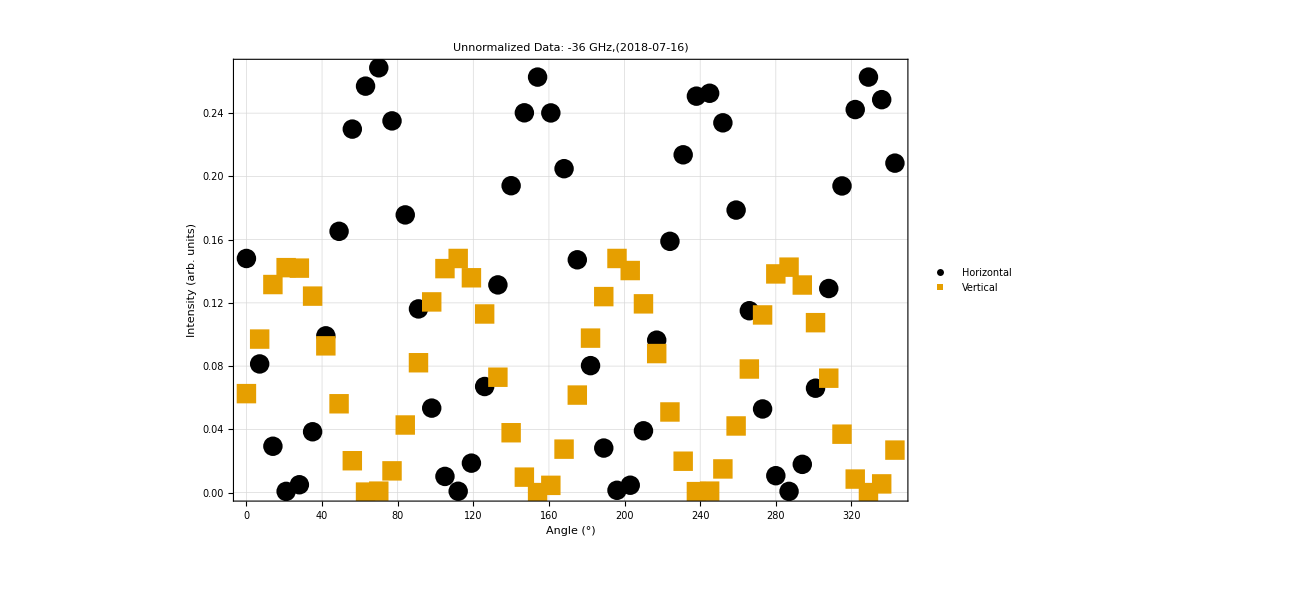

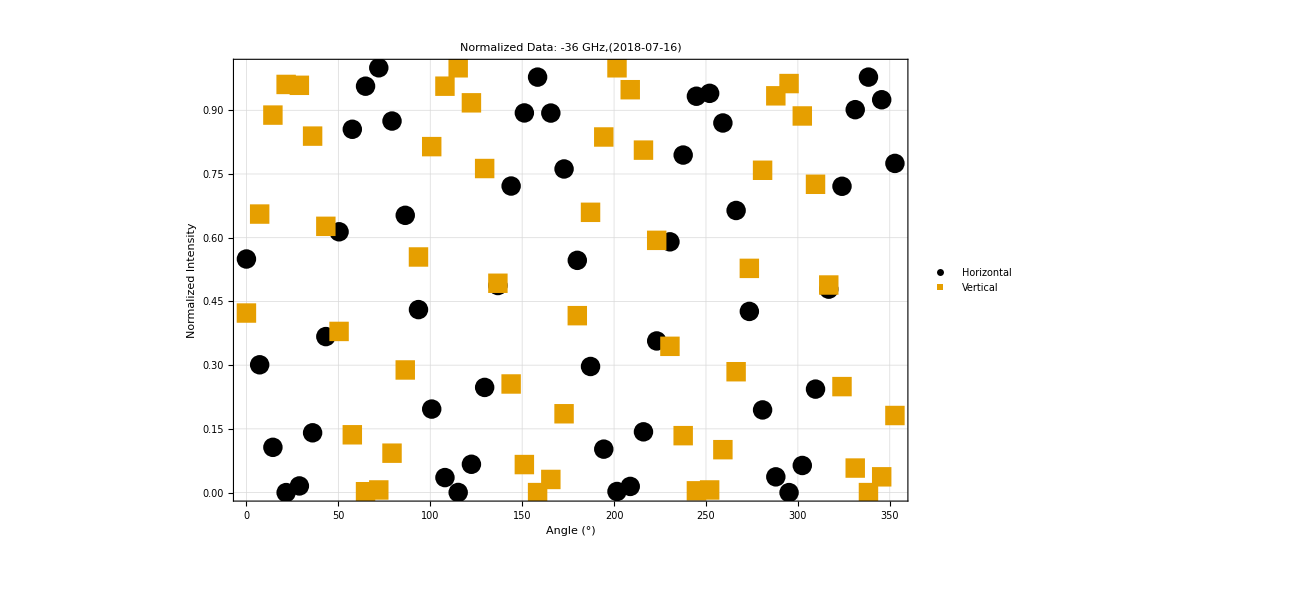

Power::infy: Infinite expression 1/0. encountered.

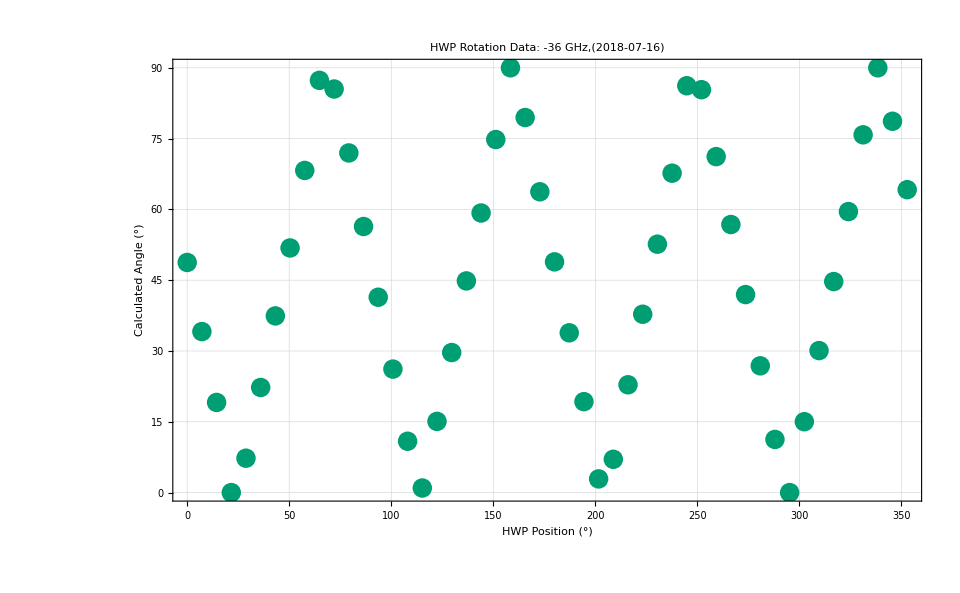

{{144/5,7.28595},{36,22.2706},{216/5,37.4316},{252/5,51.8297},{288/5,68.2539},{324/5,87.3434}}

FittedModel[-56.8964+2.193 θ]

{2.59299,0.0535871}

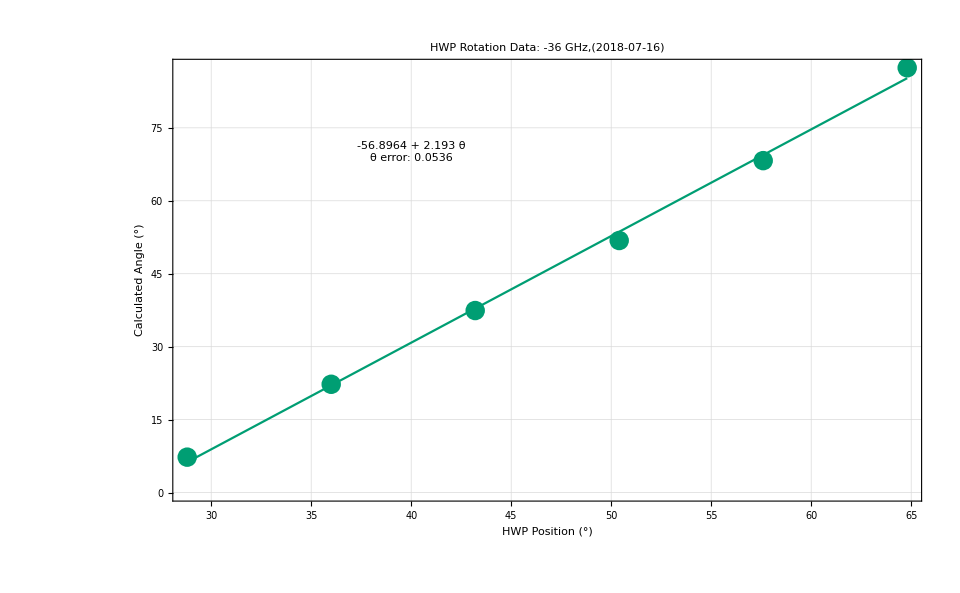

<|Slope→2.193|>

<|Slope→2.193,Slope Error→0.0535871|>

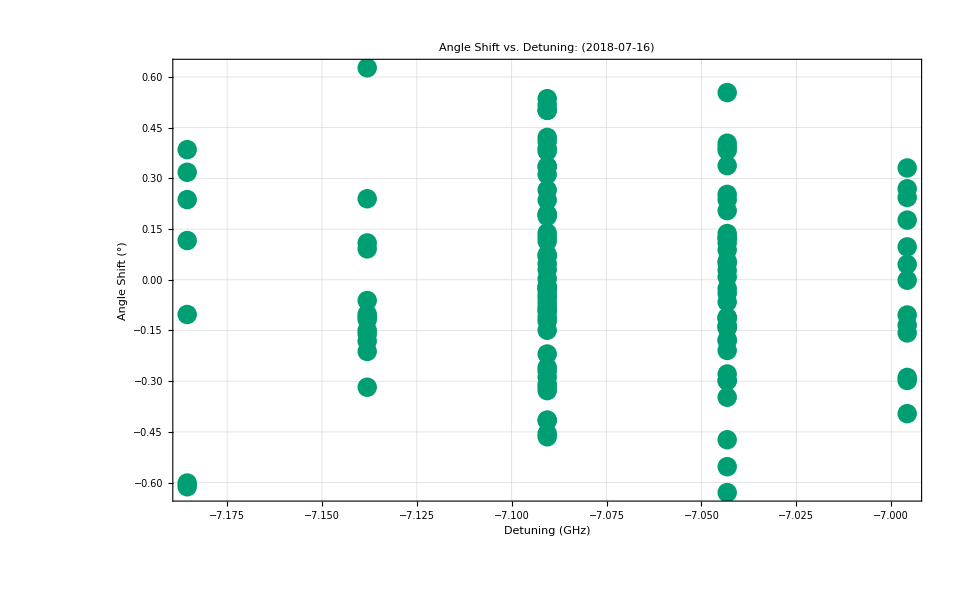

{-0.629233,0.625682}

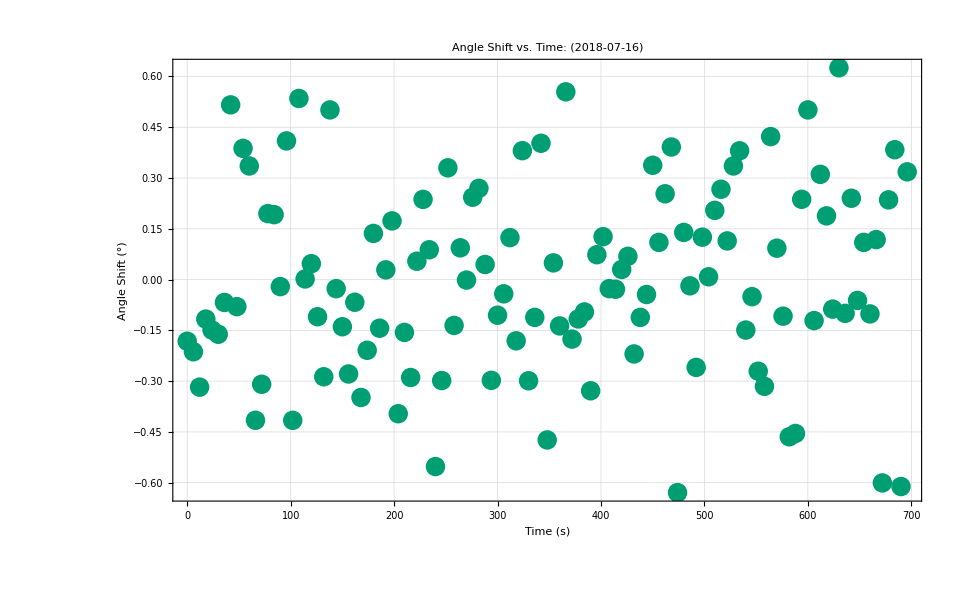

```mathematica
results=<||>;
qualifier="farDetuned";
file=ImportFile[rotationFiles[[1]]];
rawDataset=file[[2]];
headerInfo=file[[1]];
date=StringTake[headerInfo["File"],{17,26}];
(* Graph the unnormalized Data *)
rawData=Normal[Values[rawDataset[All,{"STEP","PMP","PRB"}]]];
horizontalData=Normal[Values[rawDataset[All,{"STEP","PMP"}]]];
verticalData=Normal[Values[rawDataset[All,{"STEP","PRB"}]]];
label="Unnormalized Data";
subLabel=": -36 GHz,("<>date<>")";
plotLegends={"Horizontal","Vertical"};
frameLabels={"Angle (°)","Intensity (arb. units)"};
rawDataPlot=ListPlot[{horizontalData,verticalData},PlotLabel-> label<>subLabel,PlotLegends->plotLegends,FrameLabel->frameLabels]

(* Graph the normalized Data *)
refInt=Mean[rawDataset[All,"REF"]]; (* The reference cell intensity when the measurement was made. This is used to reduce the effects of laser intensity drift on our BPD measurements *)
minPMP=Min[rawDataset[All,"PMP"]];
maxPMP=Max[rawDataset[All,"PMP"]];
minPRB=Min[rawDataset[All,"PRB"]];
maxPRB=Max[rawDataset[All,"PRB"]];
intensityNormalizedData=rawDataset[All,{#["STEP"]*360/350&,(#["PMP"]-minPMP)/(maxPMP-minPMP)&, (#["PRB"]-minPRB)/(maxPRB-minPRB)&,ArcTan[Sqrt[((#["PMP"]-minPMP)/((maxPMP-minPMP))/(#["PRB"]-minPRB)/(maxPRB-minPRB))]]&}];
hNormData=rawDataset[All,{#["STEP"]*360/350&,(#["PMP"]-minPMP)/(maxPMP-minPMP)&}];
vNormData=rawDataset[All,{#["STEP"]*360/350&,(#["PRB"]-minPRB)/(maxPRB-minPRB)&}];
label="Normalized Data";
subLabel=": -36 GHz,("<>date<>")";
plotLegends={"Horizontal","Vertical"};
frameLabels={"Angle (°)","Normalized Intensity"};
normalizedPlot=ListPlot[{hNormData,vNormData},PlotLabel-> label<>subLabel,PlotLegends->plotLegends,FrameLabel->frameLabels]


(* Graph the angle calculation data *)
angleData={};
For[i=1,i≤Length[hNormData],i++,
AppendTo[angleData,{hNormData[[i]][[1]],Check[ArcTan[Sqrt[hNormData[[i]][[2]]/vNormData[[i]][[2]]]]*180/π,90]}];
]
label="HWP Rotation Data";
plotLegends={};
subLabel=": -36 GHz,("<>date<>")";
frameLabels={"HWP Position (°)","Calculated Angle (°)"};
ListPlot[angleData,PlotLabel-> label<>subLabel,PlotLegends->plotLegends,FrameLabel->frameLabels]

linearModelData=Take[angleData,{5,10}]
lm=LinearModelFit[linearModelData,θ,θ]
lm["ParameterErrors"]
label="HWP Rotation Data";
subLabel=": -36 GHz,("<>date<>")";
plotLegends={};
frameLabels={"HWP Position (°)","Calculated Angle (°)"};
linearPlot=ListPlot[linearModelData,PlotLabel-> label<>subLabel,PlotLegends->plotLegends,FrameLabel->frameLabels];

model=Plot[lm[θ],{θ,linearModelData[[1]][[1]],linearModelData[[-1]][[1]]}];
Show[{linearPlot,model,Graphics[Text[ToString[lm["BestFit"]]<>"\nθ error: "<> ToString[NumberForm[lm["ParameterErrors"][[2]],3]],{40,70}],BaseStyle->15]}]
AppendTo[results,"Slope"->lm["BestFitParameters"][[2]]]
AppendTo[results,"Slope Error"->lm["ParameterErrors"][[2]]]

(* Detuning Graphs *)
importedFile=ImportFile[absFiles[[1]]];
absFileHeader=importedFile[[1]];
absFileData=importedFile[[2]];
date=StringTake[headerInfo["File"],{17,26}];
detData=Normal[absFileData[All,{c/100/#["WAV"]-ν0*1*^-9 &,"PMP","PRB","REF"}]];
angleData={};
For[i=1,i≤Length[detData],i++,
AppendTo[angleData,{detData[[i]][[1]],ArcTan[Sqrt[(detData[[i]][[2]]-minPMP)/(maxPMP-minPMP)/((detData[[i]][[3]]-minPRB)/(maxPRB-minPRB))]]*180/π}];
];
Transpose[angleData];
averageAngle=Mean[Transpose[angleData][[2]]];
angleShiftData=Transpose[{Transpose[angleData][[1]],Transpose[angleData][[2]]-averageAngle}];
label="Angle Shift vs. Detuning";
subLabel=": ("<>date<>")";
plotLegends={};
frameLabels={"Detuning (GHz)","Angle Shift (°)"};
shiftVsDetuningPlot=ListPlot[angleShiftData,PlotLabel-> label<>subLabel,PlotLegends->plotLegends,FrameLabel->frameLabels]

importedFile=ImportFile[absFiles[[1]]];
absFileHeader=importedFile[[1]];
absFileData=importedFile[[2]];
detData=Normal[absFileData[All,{"VOLT","PMP","PRB"}]];
angleData={};
For[i=1,i≤Length[detData],i++,
AppendTo[angleData,{detData[[i]][[1]],ArcTan[Sqrt[(detData[[i]][[2]]*refInt/detData[[i]][[3]]-minPMP)/(maxPMP-minPMP)/((detData[[i]][[3]]*refInt/detData[[i]][[3]]-minPRB)/(maxPRB-minPRB))]]*180/π}];
];
Transpose[angleData];
averageAngle=Mean[Transpose[angleData][[2]]];
angleShiftData=Transpose[{Transpose[angleData][[1]]*6,Transpose[angleData][[2]]-averageAngle}];
mM=MinMax[Transpose[angleShiftData][[2]]]

label="Angle Shift vs. Time";
subLabel=": ("<>date<>")";
plotLegends={};
frameLabels={"Time (s)","Angle Shift (°)"};
ListPlot[angleShiftData,PlotLabel-> label<>subLabel,PlotLegends->plotLegends,FrameLabel->frameLabels]

AppendTo[results,"Detuning Angle Range"->mM[[2]]-mM[[1]]];
AppendTo[results,"Angle vs. Detuning"-> shiftVsDetuningPlot];
```

## Select new Folder

```mathematica
SetDirectory[FileNameJoin[{folder,"2018-07-10_BalancedPhotoDetectorRound2","data","magnetsRound2"}]];
absFiles=FileNames[StringExpression["RbAbs",__,"_",__,DigitCharacter,".dat"]]
rotationFiles=FileNames["FDayRotation"~~RegularExpression[".{17,17}"]~~".dat"]
```

{RbAbs2018-07-17_112613.dat}

{FDayRotation2018-07-17_112426.dat,FDayRotation2018-07-17_112524.dat}

## Process Data

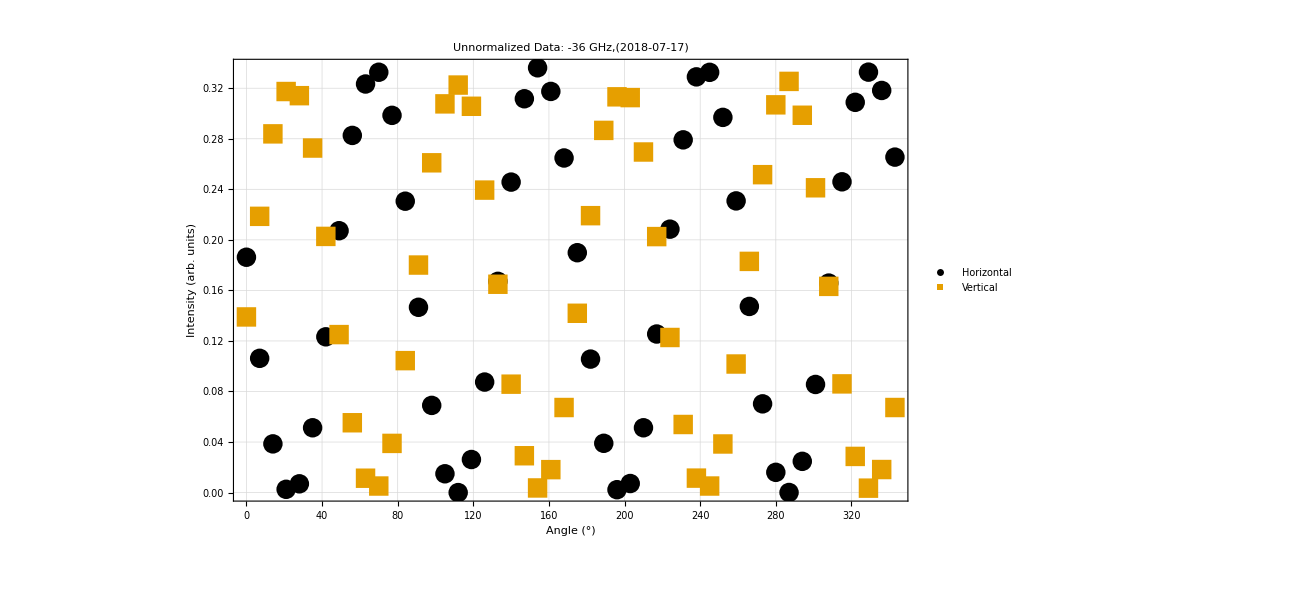

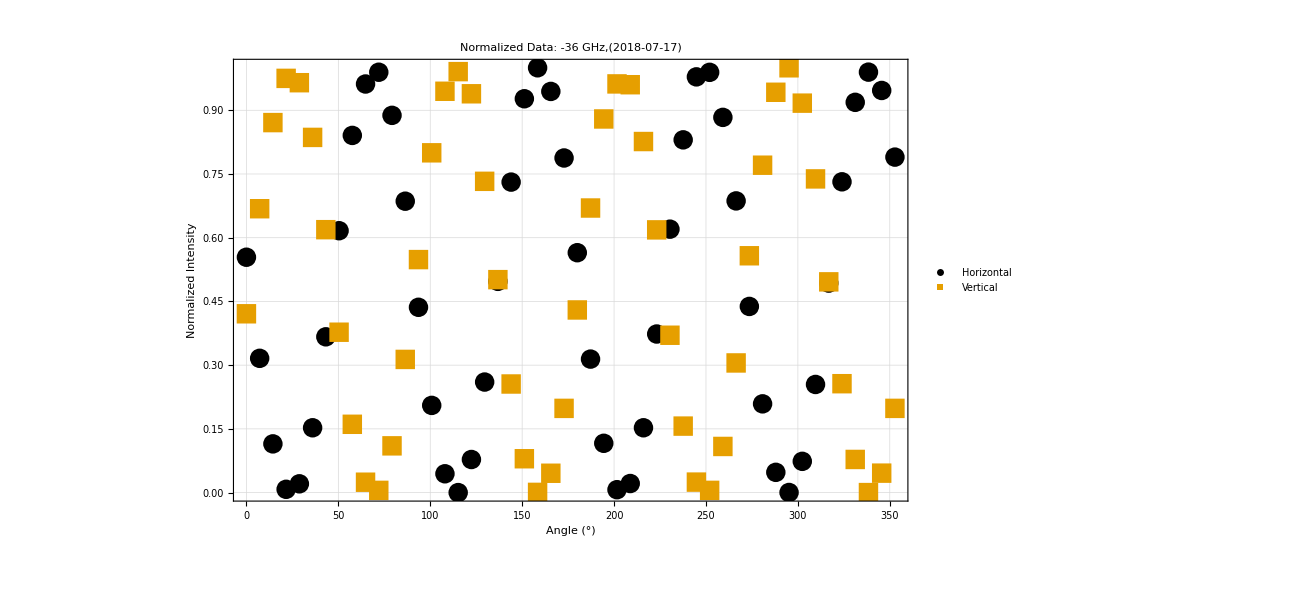

Power::infy: Infinite expression 1/0. encountered.

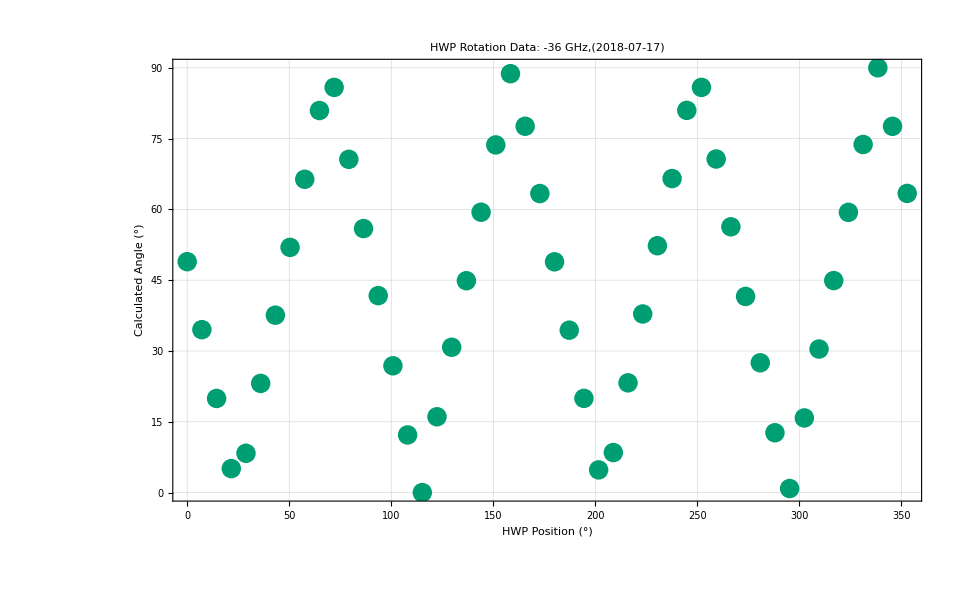

{{144/5,8.32533},{36,23.1318},{216/5,37.5869},{252/5,51.9552},{288/5,66.3811},{324/5,80.9459}}

FittedModel[-49.4768+2.01277 θ]

{0.209996,0.00433979}

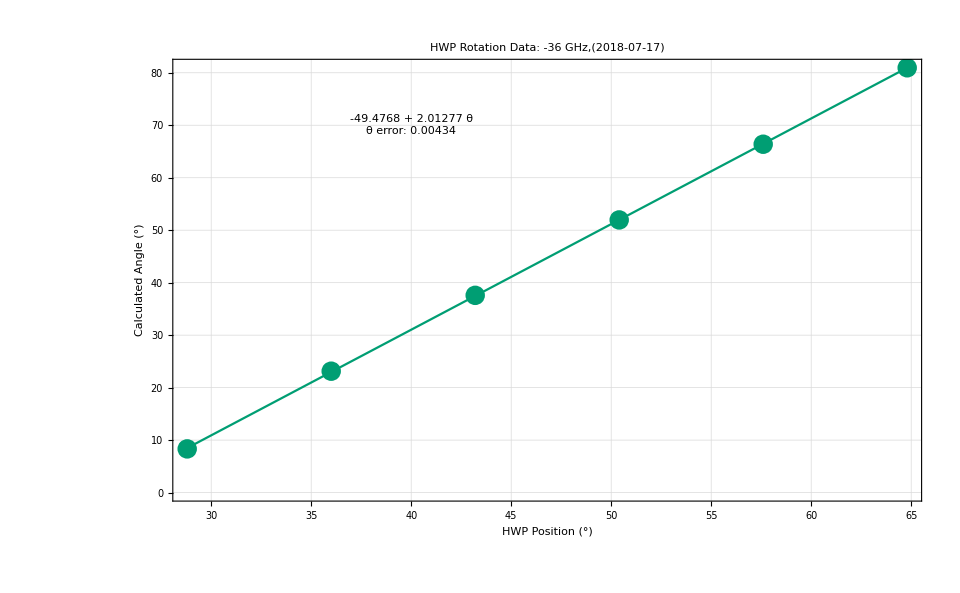

<|Slope→2.01277|>

<|Slope→2.01277,Slope Error→0.00433979|>

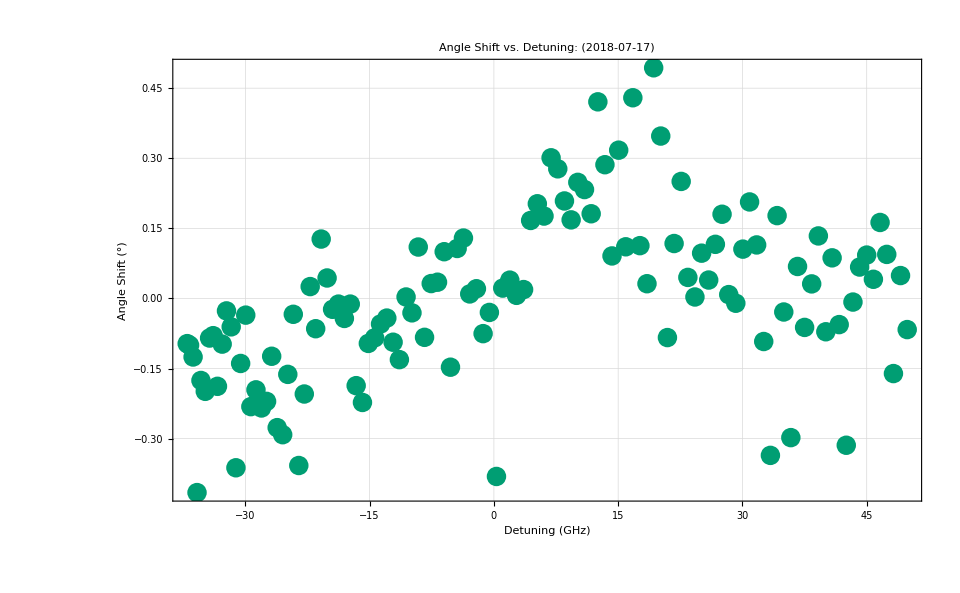

{-0.415541,0.493632}

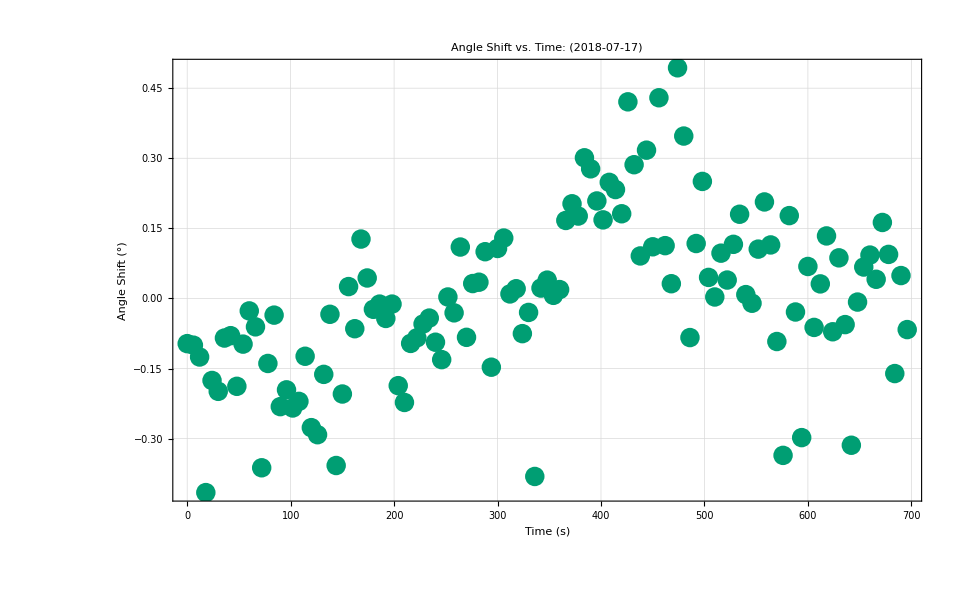

```mathematica
results=<||>;
qualifier="farDetuned";
file=ImportFile[rotationFiles[[1]]];
rawDataset=file[[2]];
headerInfo=file[[1]];
date=StringTake[headerInfo["File"],{17,26}];
(* Graph the unnormalized Data *)
rawData=Normal[Values[rawDataset[All,{"STEP","PMP","PRB"}]]];
horizontalData=Normal[Values[rawDataset[All,{"STEP","PMP"}]]];
verticalData=Normal[Values[rawDataset[All,{"STEP","PRB"}]]];
label="Unnormalized Data";
subLabel=": -36 GHz,("<>date<>")";
plotLegends={"Horizontal","Vertical"};
frameLabels={"Angle (°)","Intensity (arb. units)"};
rawDataPlot=ListPlot[{horizontalData,verticalData},PlotLabel-> label<>subLabel,PlotLegends->plotLegends,FrameLabel->frameLabels]

(* Graph the normalized Data *)
minPMP=Min[rawDataset[All,"PMP"]];
maxPMP=Max[rawDataset[All,"PMP"]];
minPRB=Min[rawDataset[All,"PRB"]];
maxPRB=Max[rawDataset[All,"PRB"]];
intensityNormalizedData=rawDataset[All,{#["STEP"]*360/350&,(#["PMP"]-minPMP)/(maxPMP-minPMP)&, (#["PRB"]-minPRB)/(maxPRB-minPRB)&,ArcTan[Sqrt[((#["PMP"]-minPMP)/((maxPMP-minPMP))/(#["PRB"]-minPRB)/(maxPRB-minPRB))]]&}];
hNormData=rawDataset[All,{#["STEP"]*360/350&,(#["PMP"]-minPMP)/(maxPMP-minPMP)&}];
vNormData=rawDataset[All,{#["STEP"]*360/350&,(#["PRB"]-minPRB)/(maxPRB-minPRB)&}];
label="Normalized Data";
subLabel=": -36 GHz,("<>date<>")";
plotLegends={"Horizontal","Vertical"};
frameLabels={"Angle (°)","Normalized Intensity"};
normalizedPlot=ListPlot[{hNormData,vNormData},PlotLabel-> label<>subLabel,PlotLegends->plotLegends,FrameLabel->frameLabels]


(* Graph the angle calculation data *)
angleData={};
For[i=1,i≤Length[hNormData],i++,
AppendTo[angleData,{hNormData[[i]][[1]],Check[ArcTan[Sqrt[hNormData[[i]][[2]]/vNormData[[i]][[2]]]]*180/π,90]}];
]
label="HWP Rotation Data";
plotLegends={};
subLabel=": -36 GHz,("<>date<>")";
frameLabels={"HWP Position (°)","Calculated Angle (°)"};
ListPlot[angleData,PlotLabel-> label<>subLabel,PlotLegends->plotLegends,FrameLabel->frameLabels]

linearModelData=Take[angleData,{5,10}]
lm=LinearModelFit[linearModelData,θ,θ]
lm["ParameterErrors"]
label="HWP Rotation Data";
subLabel=": -36 GHz,("<>date<>")";
plotLegends={};
frameLabels={"HWP Position (°)","Calculated Angle (°)"};
linearPlot=ListPlot[linearModelData,PlotLabel-> label<>subLabel,PlotLegends->plotLegends,FrameLabel->frameLabels];

model=Plot[lm[θ],{θ,linearModelData[[1]][[1]],linearModelData[[-1]][[1]]}];
Show[{linearPlot,model,Graphics[Text[ToString[lm["BestFit"]]<>"\nθ error: "<> ToString[NumberForm[lm["ParameterErrors"][[2]],3]],{40,70}],BaseStyle->15]}]
AppendTo[results,"Slope"->lm["BestFitParameters"][[2]]]
AppendTo[results,"Slope Error"->lm["ParameterErrors"][[2]]]

(* Detuning Graphs *)
importedFile=ImportFile[absFiles[[1]]];
absFileHeader=importedFile[[1]];
absFileData=importedFile[[2]];
date=StringTake[headerInfo["File"],{17,26}];
detData=Normal[absFileData[All,{c/100/#["WAV"]-ν0*1*^-9 &,"PMP","PRB","REF"}]];
angleData={};
For[i=1,i≤Length[detData],i++,
AppendTo[angleData,{detData[[i]][[1]],ArcTan[Sqrt[(detData[[i]][[2]]-minPMP)/(maxPMP-minPMP)/((detData[[i]][[3]]-minPRB)/(maxPRB-minPRB))]]*180/π}];
];
Transpose[angleData];
averageAngle=Mean[Transpose[angleData][[2]]];
angleShiftData=Transpose[{Transpose[angleData][[1]],Transpose[angleData][[2]]-averageAngle}];
label="Angle Shift vs. Detuning";
subLabel=": ("<>date<>")";
plotLegends={};
frameLabels={"Detuning (GHz)","Angle Shift (°)"};
shiftVsDetuningPlot=ListPlot[angleShiftData,PlotLabel-> label<>subLabel,PlotLegends->plotLegends,FrameLabel->frameLabels]

importedFile=ImportFile[absFiles[[1]]];
absFileHeader=importedFile[[1]];
absFileData=importedFile[[2]];
voltData=Normal[absFileData[All,{"VOLT","PMP","PRB"}]];
angleData={};
For[i=1,i≤Length[voltData],i++,
AppendTo[angleData,{voltData[[i]][[1]],ArcTan[Sqrt[(voltData[[i]][[2]]-minPMP)/(maxPMP-minPMP)/((voltData[[i]][[3]]-minPRB)/(maxPRB-minPRB))]]*180/π}];
];
Transpose[angleData];
averageAngle=Mean[Transpose[angleData][[2]]];
angleShiftData=Transpose[{Transpose[angleData][[1]]*6,Transpose[angleData][[2]]-averageAngle}];
mM=MinMax[Transpose[angleShiftData][[2]]]

label="Angle Shift vs. Time";
subLabel=": ("<>date<>")";
plotLegends={};
frameLabels={"Time (s)","Angle Shift (°)"};
ListPlot[angleShiftData,PlotLabel-> label<>subLabel,PlotLegends->plotLegends,FrameLabel->frameLabels]

AppendTo[results,"Detuning Angle Range"->mM[[2]]-mM[[1]]];
AppendTo[results,"Angle vs. Detuning"-> shiftVsDetuningPlot];
```

## Warmed Cell Data

{RbAbs2018-07-17_164828.dat}

{FDayRotation2018-07-17_164637.dat,FDayRotation2018-07-17_164740.dat}

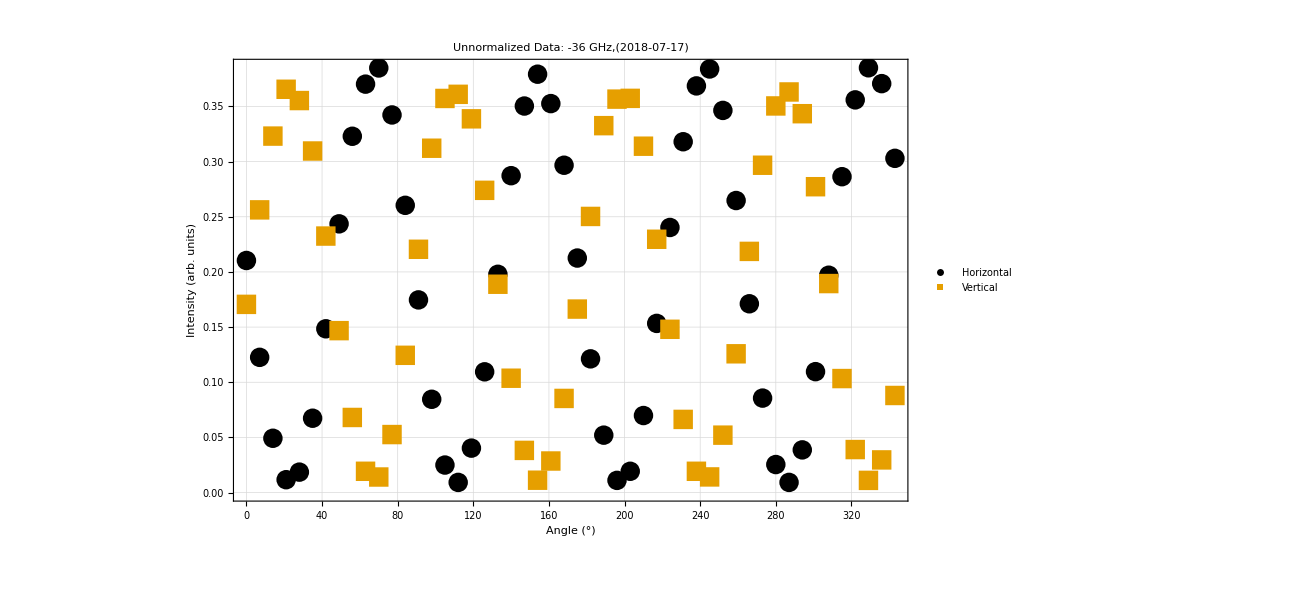

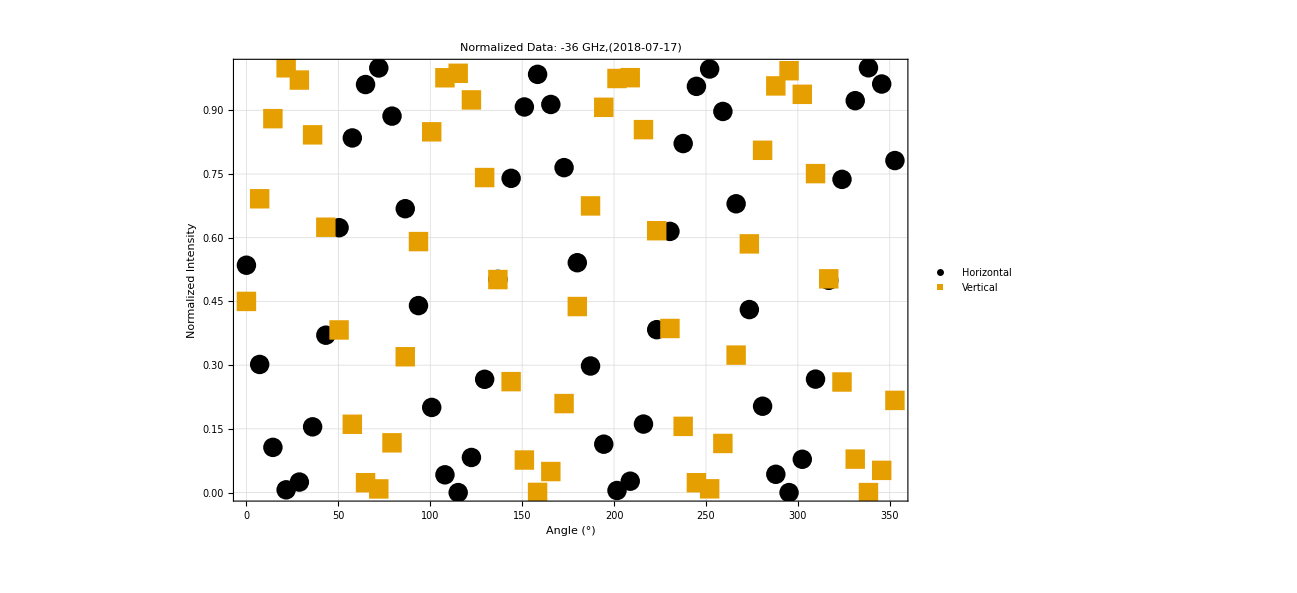

Power::infy: Infinite expression 1/0. encountered.

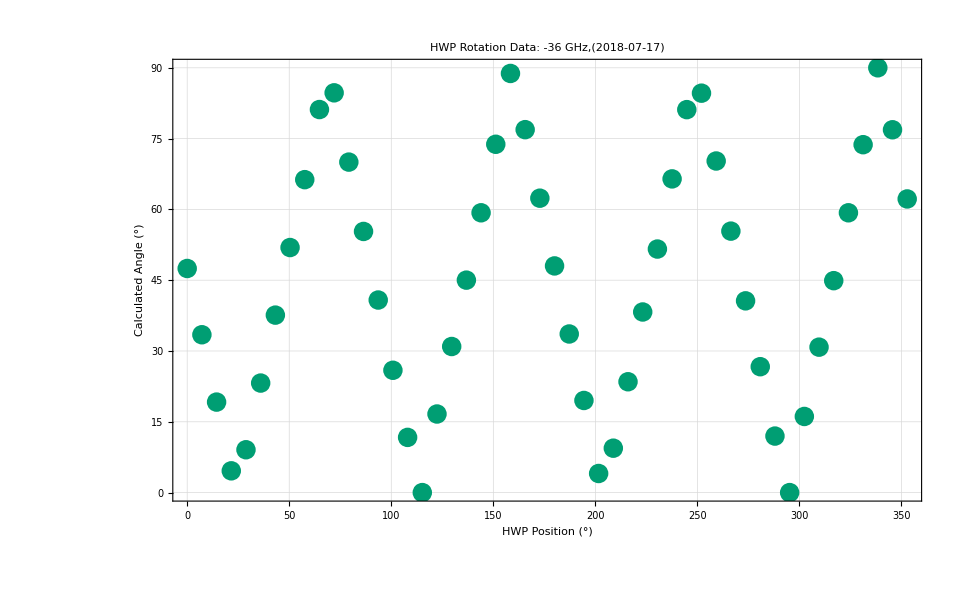

{{144/5,9.07573},{36,23.2053},{216/5,37.6013},{252/5,51.9196},{288/5,66.3013},{324/5,81.1558}}

FittedModel[-48.7248+2.00003 θ]

{0.344349,0.00711635}

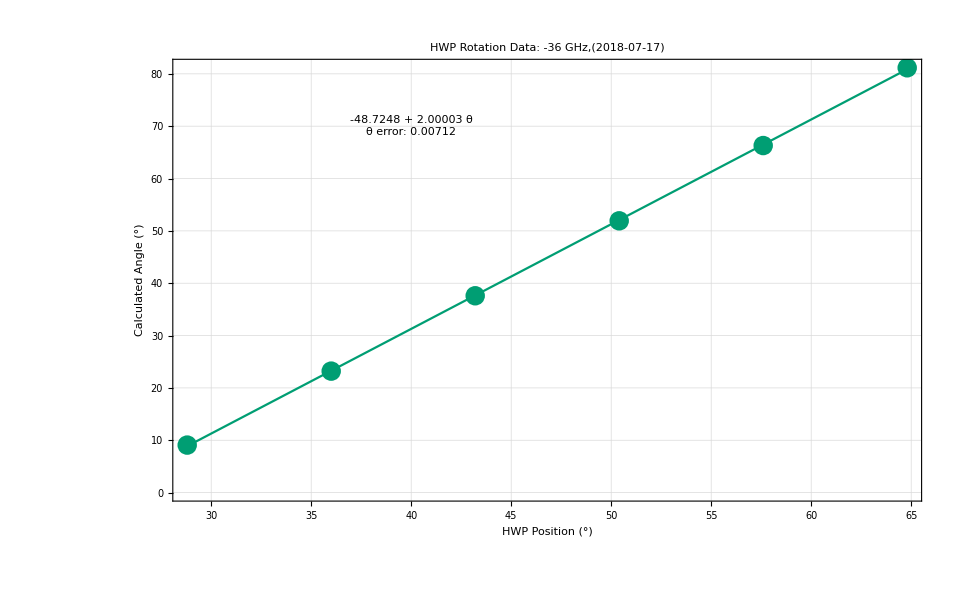

<|Slope→2.00003|>

<|Slope→2.00003,Slope Error→0.00711635|>

Dataset[<>]

{{-36.8771,-1.85291},{-36.5925,-1.11636},{-36.1657,-1.66842},{-35.6914,-1.67201},{-35.2171,-2.0263},{-34.6954,-1.2336},{-34.1737,-1.21456},{-33.652,-1.70609},{-33.1303,-1.58818},{-32.6086,-1.45611},{-32.0395,-1.50982},{-31.5178,-1.55702},{-30.9486,-1.73216},{-30.3321,-1.37616},{-29.7629,-1.31128},{-29.1463,-1.18901},{-28.5298,-1.47533},{-27.9132,-1.35679},{-27.2966,-1.10996},{-26.68,-1.41794},{-26.016,-1.45477},{-25.352,-1.38625},{-24.7354,-1.07119},{-24.0714,-1.09732},{-23.4074,-1.24658},{-22.7433,-1.41101},{-22.0319,-0.99602},{-21.3679,-1.19496},{-20.6564,-1.04269},{-19.9449,-0.999284},{-19.2809,-1.29887},{-18.5694,-0.95811},{-17.8579,-0.839103},{-17.1465,-0.524416},{-16.3876,-0.865814},{-15.6761,-0.393703},{-14.9646,-0.0791038},{-14.2057,-0.375938},{-13.4942,0.22122},{-12.7353,0.0607423},{-11.9763,0.726333},{-11.2174,0.634983},{-10.4585,0.967184},{-9.69952,1.48337},{-8.94058,1.79407},{-8.18163,2.78498},{-5.85735,4.51917},{-5.05096,4.53652},{-4.292,3.19752},{6.23889,14.3566},{7.09277,14.5201},{7.89921,10.4714},{8.70566,8.03225},{9.607,6.03273},{10.4135,4.27495},{11.2199,3.2783},{12.0264,2.16117},{12.8803,2.14123},{13.7342,1.59905},{14.5407,1.26146},{15.3472,0.773804},{16.2011,0.641402},{17.0076,-0.0220127},{17.814,0.06272},{18.6205,0.0791266},{19.4745,-0.0809231},{20.3284,-0.384036},{21.1349,-0.276451},{21.9889,-0.690909},{22.8903,-0.489256},{23.6968,-0.696534},{24.5507,-1.50884},{25.3573,-0.651765},{26.1638,-0.797031},{27.0178,-1.0803},{27.8243,-0.722959},{28.6308,-0.985672},{29.4848,-1.11362},{30.3388,-1.41601},{31.0979,-1.2832},{31.9519,-1.21376},{32.8059,-1.05587},{33.6124,-1.50881},{34.4665,-1.38953},{35.273,-1.14497},{36.127,-0.815735},{36.981,-1.2525},{37.7876,-1.39091},{38.5942,-1.35011},{39.4482,-1.24971},{40.3023,-1.56282},{41.1088,-1.87678},{41.9154,-1.2785},{42.7695,-1.65285},{43.6235,-1.35293},{44.4301,-1.69738},{45.2842,-1.38266},{46.0908,-1.48493},{46.8974,-1.71011},{47.704,-1.23317},{48.5581,-1.30839},{49.4122,-1.43638},{50.2188,-1.25896}}

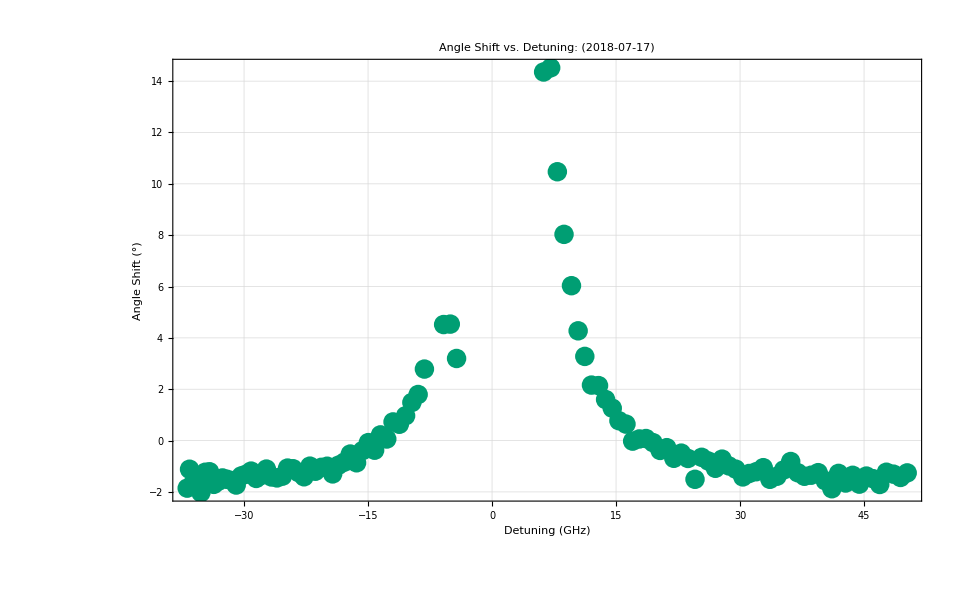

{-29.1896,24.5781}

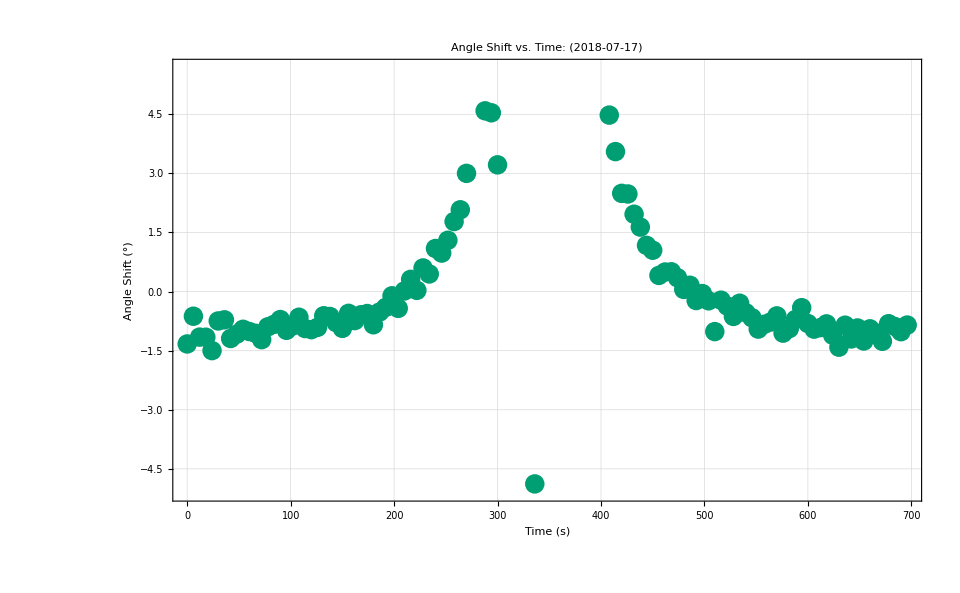

```mathematica
SetDirectory[FileNameJoin[{folder,"2018-07-10_BalancedPhotoDetectorRound2","data","warmedCell"}]];
absFiles=FileNames[StringExpression["RbAbs",__,"_",__,DigitCharacter,".dat"]]
rotationFiles=FileNames["FDayRotation"~~RegularExpression[".{17,17}"]~~".dat"]

results=<||>;
qualifier="farDetuned";
file=ImportFile[rotationFiles[[1]]];
rawDataset=file[[2]];
headerInfo=file[[1]];
date=StringTake[headerInfo["File"],{17,26}];
(* Graph the unnormalized Data *)
rawData=Normal[Values[rawDataset[All,{"STEP","PMP","PRB"}]]];
horizontalData=Normal[Values[rawDataset[All,{"STEP","PMP"}]]];
verticalData=Normal[Values[rawDataset[All,{"STEP","PRB"}]]];
label="Unnormalized Data";
subLabel=": -36 GHz,("<>date<>")";
plotLegends={"Horizontal","Vertical"};
frameLabels={"Angle (°)","Intensity (arb. units)"};
rawDataPlot=ListPlot[{horizontalData,verticalData},PlotLabel-> label<>subLabel,PlotLegends->plotLegends,FrameLabel->frameLabels]

(* Graph the normalized Data *)
refInt=Mean[rawDataset[All,"REF"]]; (* The reference cell intensity when the measurement was made. This is used to reduce the effects of laser intensity drift on our BPD measurements *)
minPMP=Min[rawDataset[All,"PMP"]];
maxPMP=Max[rawDataset[All,"PMP"]];
minPRB=Min[rawDataset[All,"PRB"]];
maxPRB=Max[rawDataset[All,"PRB"]];
intensityNormalizedData=rawDataset[All,{#["STEP"]*360/350&,(#["PMP"]-minPMP)/(maxPMP-minPMP)&, (#["PRB"]-minPRB)/(maxPRB-minPRB)&,ArcTan[Sqrt[((#["PMP"]-minPMP)/((maxPMP-minPMP))/(#["PRB"]-minPRB)/(maxPRB-minPRB))]]&}];
hNormData=rawDataset[All,{#["STEP"]*360/350&,(#["PMP"]-minPMP)/(maxPMP-minPMP)&}];
vNormData=rawDataset[All,{#["STEP"]*360/350&,(#["PRB"]-minPRB)/(maxPRB-minPRB)&}];
label="Normalized Data";
subLabel=": -36 GHz,("<>date<>")";
plotLegends={"Horizontal","Vertical"};
frameLabels={"Angle (°)","Normalized Intensity"};
normalizedPlot=ListPlot[{hNormData,vNormData},PlotLabel-> label<>subLabel,PlotLegends->plotLegends,FrameLabel->frameLabels]


(* Graph the angle calculation data *)
angleData={};
For[i=1,i≤Length[hNormData],i++,
AppendTo[angleData,{hNormData[[i]][[1]],Check[ArcTan[Sqrt[hNormData[[i]][[2]]/vNormData[[i]][[2]]]]*180/π,90]}];
]
label="HWP Rotation Data";
plotLegends={};
subLabel=": -36 GHz,("<>date<>")";
frameLabels={"HWP Position (°)","Calculated Angle (°)"};
ListPlot[angleData,PlotLabel-> label<>subLabel,PlotLegends->plotLegends,FrameLabel->frameLabels]

linearModelData=Take[angleData,{5,10}]
lm=LinearModelFit[linearModelData,θ,θ]
lm["ParameterErrors"]
label="HWP Rotation Data";
subLabel=": -36 GHz,("<>date<>")";
plotLegends={};
frameLabels={"HWP Position (°)","Calculated Angle (°)"};
linearPlot=ListPlot[linearModelData,PlotLabel-> label<>subLabel,PlotLegends->plotLegends,FrameLabel->frameLabels];

model=Plot[lm[θ],{θ,linearModelData[[1]][[1]],linearModelData[[-1]][[1]]}];
Show[{linearPlot,model,Graphics[Text[ToString[lm["BestFit"]]<>"\nθ error: "<> ToString[NumberForm[lm["ParameterErrors"][[2]],3]],{40,70}],BaseStyle->15]}]
AppendTo[results,"Slope"->lm["BestFitParameters"][[2]]]
AppendTo[results,"Slope Error"->lm["ParameterErrors"][[2]]]

(* Detuning Graphs *)
importedFile=ImportFile[absFiles[[1]]];
absFileHeader=importedFile[[1]];
absFileData=importedFile[[2]];
date=StringTake[headerInfo["File"],{17,26}];
absFileDataLong=Select[absFileData,#WAV>794.9872844&];
absFileDataShort=Select[absFileData,#WAV<794.9662036&];
absFileData=Join[absFileDataLong,absFileDataShort];
detData=Normal[absFileData[All,{c/100/#["WAV"]-ν0*1*^-9 &,"PMP","PRB","REF"}],]
angleData={};
For[i=1,i≤Length[detData],i++,
AppendTo[angleData,{detData[[i]][[1]],ArcTan[Sqrt[(detData[[i]][[2]]-minPMP)/(maxPMP-minPMP)/((detData[[i]][[3]]-minPRB)/(maxPRB-minPRB))]]*180/π}];
];
Transpose[angleData];
averageAngle=Mean[Transpose[angleData][[2]]];
angleShiftData=Transpose[{Transpose[angleData][[1]],Transpose[angleData][[2]]-averageAngle}]
label="Angle Shift vs. Detuning";
subLabel=": ("<>date<>")";
plotLegends={};
frameLabels={"Detuning (GHz)","Angle Shift (°)"};
shiftVsDetuningPlot=ListPlot[angleShiftData,PlotLabel-> label<>subLabel,PlotLegends->plotLegends,FrameLabel->frameLabels,PlotRange->Full]

importedFile=ImportFile[absFiles[[1]]];
absFileHeader=importedFile[[1]];
absFileData=importedFile[[2]];
detData=Normal[absFileData[All,{"VOLT","PMP","PRB"}]];
angleData={};
For[i=1,i≤Length[detData],i++,
AppendTo[angleData,{detData[[i]][[1]],ArcTan[Sqrt[(detData[[i]][[2]]*refInt/detData[[i]][[3]]-minPMP)/(maxPMP-minPMP)/((detData[[i]][[3]]*refInt/detData[[i]][[3]]-minPRB)/(maxPRB-minPRB))]]*180/π}];
];
Transpose[angleData];
averageAngle=Mean[Transpose[angleData][[2]]];
angleShiftData=Transpose[{Transpose[angleData][[1]]*6,Transpose[angleData][[2]]-averageAngle}];
mM=MinMax[Transpose[angleShiftData][[2]]]

label="Angle Shift vs. Time";
subLabel=": ("<>date<>")";
plotLegends={};
frameLabels={"Time (s)","Angle Shift (°)"};
ListPlot[angleShiftData,PlotLabel-> label<>subLabel,PlotLegends->plotLegends,FrameLabel->frameLabels]

AppendTo[results,"Detuning Angle Range"->mM[[2]]-mM[[1]]];
AppendTo[results,"Angle vs. Detuning"-> shiftVsDetuningPlot];
```

## New stuff

```mathematica
newDirectory=FileNameJoin[{folder,"2018-08-06_excitationFunctionStudyRbCompare","data","findingn_Rb"}]
SetDirectory[newDirectory];
dataset=SemanticImport["faradayOrderedPairs.csv"];
ordPairs=Normal[dataset[All,Values]];
a2=CalculateA2FittingParameter[ordPairs];
CalculateNumberDensity[a2,290]
```

C:\Users\kahrendsen2\Dropbox\00School\research\DataRuns\2018-08-06_excitationFunctionStudyRbCompare\data\findingn_Rb

2.17589×10^15

## Magnets Off, Cell Warm

{RbAbs2018-07-17_192629.dat}

{FDayRotation2018-07-17_192439.dat,FDayRotation2018-07-17_192542.dat}

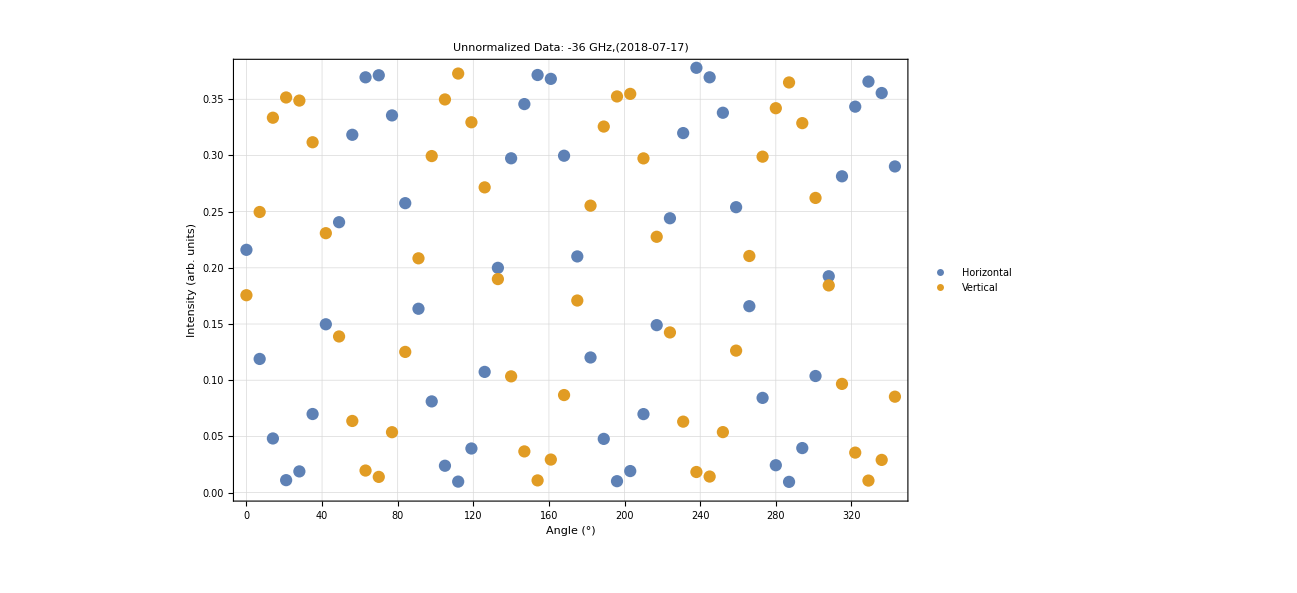

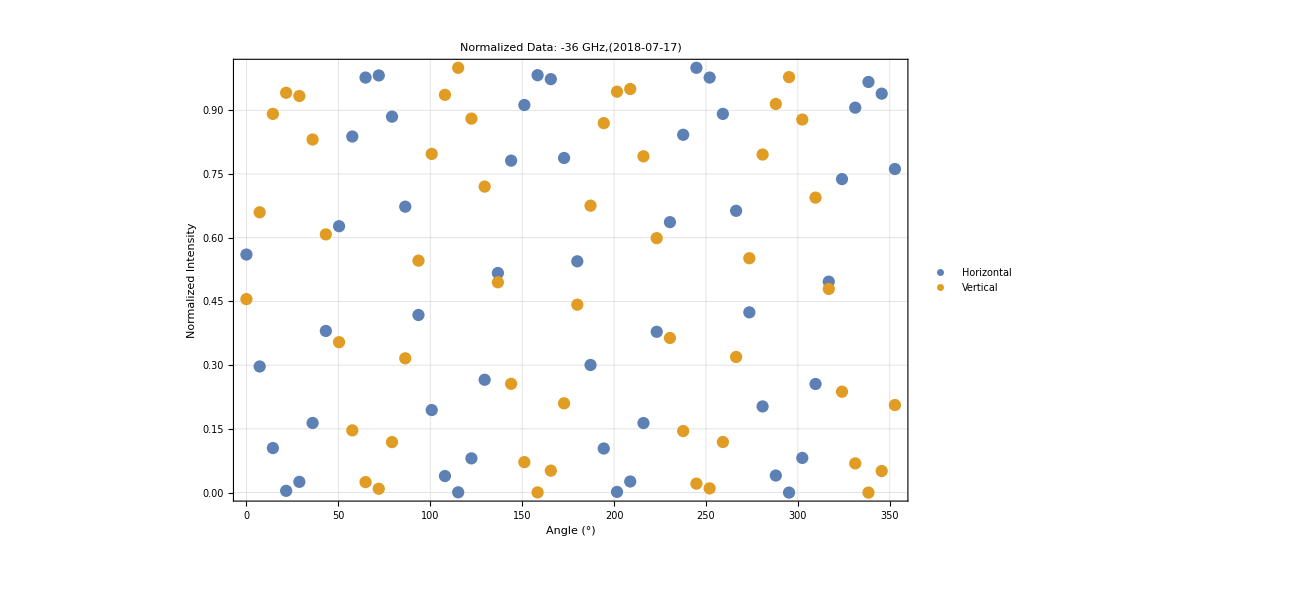

Power::infy: Infinite expression 1/0. encountered.

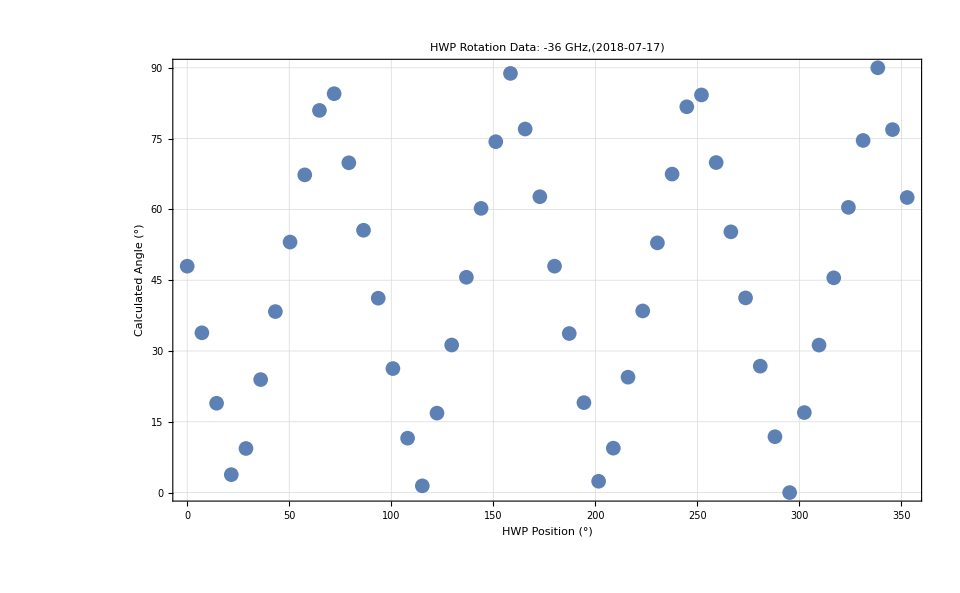

{{144/5,9.34371},{36,23.942},{216/5,38.3543},{252/5,53.0789},{288/5,67.3138},{324/5,80.9731}}

FittedModel[-47.9109+1.99598 θ]

{0.557343,0.0115181}

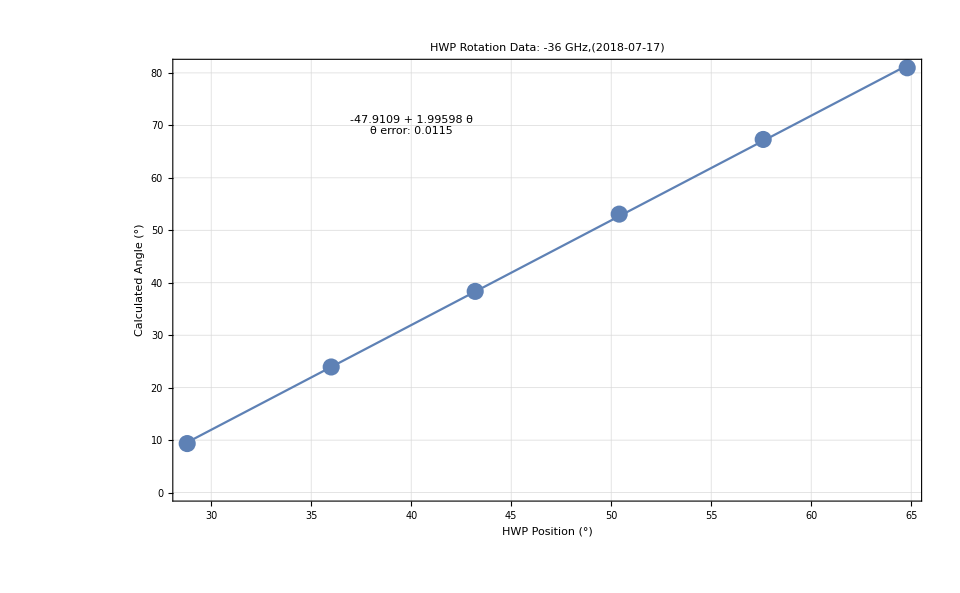

<|Slope→1.99598|>

<|Slope→1.99598,Slope Error→0.0115181|>

Dataset[<>]

{{-36.8297,-0.620061},{-36.5451,-0.341659},{-36.1183,-0.490289},{-35.6914,0.0667159},{-35.1697,-0.260315},{-34.648,-0.382807},{-34.1263,-0.4452},{-33.652,-0.387995},{-33.0829,0.0958122},{-32.5612,-0.30347},{-31.992,-0.64639},{-31.4229,-0.646251},{-30.8063,-0.259518},{-30.1898,0.259972},{-29.6206,-1.04002},{-29.0041,-0.0488543},{-28.3875,-0.415384},{-27.7709,-0.847432},{-27.1543,-0.0560946},{-26.5377,0.109659},{-25.9212,-0.433863},{-25.2571,-0.159691},{-24.6405,-0.0799219},{-23.9765,0.0540596},{-23.3125,-0.292315},{-22.601,-0.646584},{-21.8896,-0.18411},{-21.2256,-0.204131},{-20.5615,-0.245206},{-19.8501,0.19294},{-19.2335,-0.230301},{-18.522,0.0924003},{-17.8105,-0.222398},{-17.099,0.0124076},{-16.3876,0.099915},{-15.6761,0.239658},{-14.9646,-0.395771},{-14.2531,-0.00988223},{-13.4942,0.116712},{-12.7353,-0.0691577},{-11.9289,-0.606425},{-11.17,-0.22523},{-10.411,0.351751},{-9.65208,0.434188},{-8.94058,-0.228088},{-8.18163,-0.142949},{-7.47012,-0.544243},{-6.6163,-0.234634},{-5.85735,-0.848445},{-5.09839,-1.56375},{-4.292,-1.53195},{6.28632,1.15757},{7.14021,0.673239},{7.89921,0.19972},{8.70566,0.552371},{9.55956,0.466007},{10.366,0.462507},{11.2199,0.502859},{11.9789,0.534648},{12.7854,0.13306},{13.6868,-0.14865},{14.4932,0.679928},{15.2997,0.235931},{16.1536,0.178644},{16.9601,0.216533},{17.814,0.360819},{18.6205,0.269829},{19.427,0.263823},{20.281,0.256826},{21.0875,-0.0482739},{21.894,-0.052251},{22.7005,-0.17599},{23.5545,0.993078},{24.361,0.10825},{25.2149,0.247636},{25.974,-0.0736244},{26.828,0.283636},{27.682,0.521967},{28.5359,0.0813676},{29.3899,0.321766},{30.2439,0.094189},{31.0979,1.14793},{31.9044,-0.156988},{32.7584,0.179644},{33.565,0.380349},{34.419,0.188661},{35.2256,0.212073},{36.0796,0.911929},{36.8862,-0.129557},{37.6927,-0.315592},{38.5468,0.189108},{39.3533,0.0945127},{40.2074,0.00919618},{41.0614,0.241097},{41.868,0.23986},{42.722,-0.199357},{43.5286,-0.252459},{44.3352,-0.0481052},{45.1893,0.719508},{45.9959,0.159277},{46.85,-0.089969},{47.6566,0.528046},{48.5106,0.219824},{49.3173,0.462405},{50.1239,0.175784}}

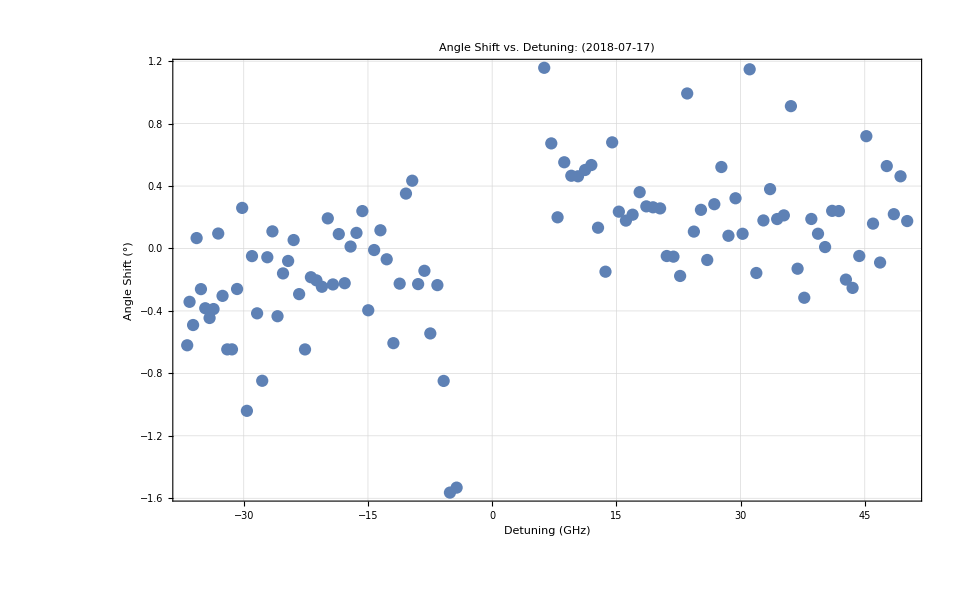

{-12.4963,8.33387}

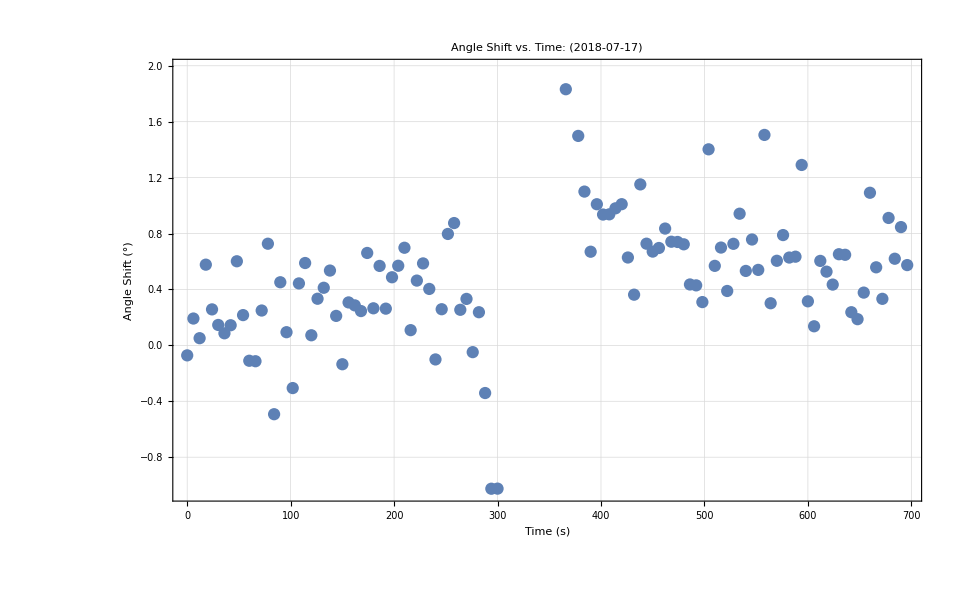

```mathematica
SetDirectory[FileNameJoin[{folder,"2018-07-10_BalancedPhotoDetectorRound2","data","magnetsOffCellWarm"}]];
absFiles=FileNames[StringExpression["RbAbs",__,"_",__,DigitCharacter,".dat"]]
rotationFiles=FileNames["FDayRotation"~~RegularExpression[".{17,17}"]~~".dat"]

results=<||>;
qualifier="farDetuned";
file=ImportFile[rotationFiles[[1]]];
rawDataset=file[[2]];
headerInfo=file[[1]];
date=StringTake[headerInfo["File"],{17,26}];
(* Graph the unnormalized Data *)
rawData=Normal[Values[rawDataset[All,{"STEP","PMP","PRB"}]]];
horizontalData=Normal[Values[rawDataset[All,{"STEP","PMP"}]]];
verticalData=Normal[Values[rawDataset[All,{"STEP","PRB"}]]];
label="Unnormalized Data";
subLabel=": -36 GHz,("<>date<>")";
plotLegends={"Horizontal","Vertical"};
frameLabels={"Angle (°)","Intensity (arb. units)"};
rawDataPlot=ListPlot[{horizontalData,verticalData},PlotLabel-> label<>subLabel,PlotLegends->plotLegends,FrameLabel->frameLabels]

(* Graph the normalized Data *)
refInt=Mean[rawDataset[All,"REF"]]; (* The reference cell intensity when the measurement was made. This is used to reduce the effects of laser intensity drift on our BPD measurements *)
minPMP=Min[rawDataset[All,"PMP"]];
maxPMP=Max[rawDataset[All,"PMP"]];
minPRB=Min[rawDataset[All,"PRB"]];
maxPRB=Max[rawDataset[All,"PRB"]];
intensityNormalizedData=rawDataset[All,{#["STEP"]*360/350&,(#["PMP"]-minPMP)/(maxPMP-minPMP)&, (#["PRB"]-minPRB)/(maxPRB-minPRB)&,ArcTan[Sqrt[((#["PMP"]-minPMP)/((maxPMP-minPMP))/(#["PRB"]-minPRB)/(maxPRB-minPRB))]]&}];
hNormData=rawDataset[All,{#["STEP"]*360/350&,(#["PMP"]-minPMP)/(maxPMP-minPMP)&}];
vNormData=rawDataset[All,{#["STEP"]*360/350&,(#["PRB"]-minPRB)/(maxPRB-minPRB)&}];
label="Normalized Data";
subLabel=": -36 GHz,("<>date<>")";
plotLegends={"Horizontal","Vertical"};
frameLabels={"Angle (°)","Normalized Intensity"};
normalizedPlot=ListPlot[{hNormData,vNormData},PlotLabel-> label<>subLabel,PlotLegends->plotLegends,FrameLabel->frameLabels]


(* Graph the angle calculation data *)
angleData={};
For[i=1,i≤Length[hNormData],i++,
AppendTo[angleData,{hNormData[[i]][[1]],Check[ArcTan[Sqrt[hNormData[[i]][[2]]/vNormData[[i]][[2]]]]*180/π,90]}];
]
label="HWP Rotation Data";
plotLegends={};
subLabel=": -36 GHz,("<>date<>")";
frameLabels={"HWP Position (°)","Calculated Angle (°)"};
ListPlot[angleData,PlotLabel-> label<>subLabel,PlotLegends->plotLegends,FrameLabel->frameLabels]

linearModelData=Take[angleData,{5,10}]
lm=LinearModelFit[linearModelData,θ,θ]
lm["ParameterErrors"]
label="HWP Rotation Data";
subLabel=": -36 GHz,("<>date<>")";
plotLegends={};
frameLabels={"HWP Position (°)","Calculated Angle (°)"};
linearPlot=ListPlot[linearModelData,PlotLabel-> label<>subLabel,PlotLegends->plotLegends,FrameLabel->frameLabels];

model=Plot[lm[θ],{θ,linearModelData[[1]][[1]],linearModelData[[-1]][[1]]}];
Show[{linearPlot,model,Graphics[Text[ToString[lm["BestFit"]]<>"\nθ error: "<> ToString[NumberForm[lm["ParameterErrors"][[2]],3]],{40,70}],BaseStyle->15]}]
AppendTo[results,"Slope"->lm["BestFitParameters"][[2]]]
AppendTo[results,"Slope Error"->lm["ParameterErrors"][[2]]]

(* Detuning Graphs *)
importedFile=ImportFile[absFiles[[1]]];
absFileHeader=importedFile[[1]];
absFileData=importedFile[[2]];
date=StringTake[headerInfo["File"],{17,26}];
absFileDataLong=Select[absFileData,#WAV>794.9872844&];
absFileDataShort=Select[absFileData,#WAV<794.9662036&];
absFileData=Join[absFileDataLong,absFileDataShort];
detData=Normal[absFileData[All,{c/100/#["WAV"]-ν0*1*^-9 &,"PMP","PRB","REF"}],]
angleData={};
For[i=1,i≤Length[detData],i++,
AppendTo[angleData,{detData[[i]][[1]],ArcTan[Sqrt[(detData[[i]][[2]]-minPMP)/(maxPMP-minPMP)/((detData[[i]][[3]]-minPRB)/(maxPRB-minPRB))]]*180/π}];
];
Transpose[angleData];
averageAngle=Mean[Transpose[angleData][[2]]];
angleShiftData=Transpose[{Transpose[angleData][[1]],Transpose[angleData][[2]]-averageAngle}]
label="Angle Shift vs. Detuning";
subLabel=": ("<>date<>")";
plotLegends={};
frameLabels={"Detuning (GHz)","Angle Shift (°)"};
shiftVsDetuningPlot=ListPlot[angleShiftData,PlotLabel-> label<>subLabel,PlotLegends->plotLegends,FrameLabel->frameLabels,PlotRange->Full]

importedFile=ImportFile[absFiles[[1]]];
absFileHeader=importedFile[[1]];
absFileData=importedFile[[2]];
detData=Normal[absFileData[All,{"VOLT","PMP","PRB"}]];
angleData={};
For[i=1,i≤Length[detData],i++,
AppendTo[angleData,{detData[[i]][[1]],ArcTan[Sqrt[(detData[[i]][[2]]*refInt/detData[[i]][[3]]-minPMP)/(maxPMP-minPMP)/((detData[[i]][[3]]*refInt/detData[[i]][[3]]-minPRB)/(maxPRB-minPRB))]]*180/π}];
];
Transpose[angleData];
averageAngle=Mean[Transpose[angleData][[2]]];
angleShiftData=Transpose[{Transpose[angleData][[1]]*6,Transpose[angleData][[2]]-averageAngle}];
mM=MinMax[Transpose[angleShiftData][[2]]]

label="Angle Shift vs. Time";
subLabel=": ("<>date<>")";
plotLegends={};
frameLabels={"Time (s)","Angle Shift (°)"};
ListPlot[angleShiftData,PlotLabel-> label<>subLabel,PlotLegends->plotLegends,FrameLabel->frameLabels]

AppendTo[results,"Detuning Angle Range"->mM[[2]]-mM[[1]]];
AppendTo[results,"Angle vs. Detuning"-> shiftVsDetuningPlot];
```

## Magnets off, cell warm, laser clipped

{FScanBPD2018-07-18_112258.dat}

{FDayRotation2018-07-18_112111.dat,FDayRotation2018-07-18_112210.dat}

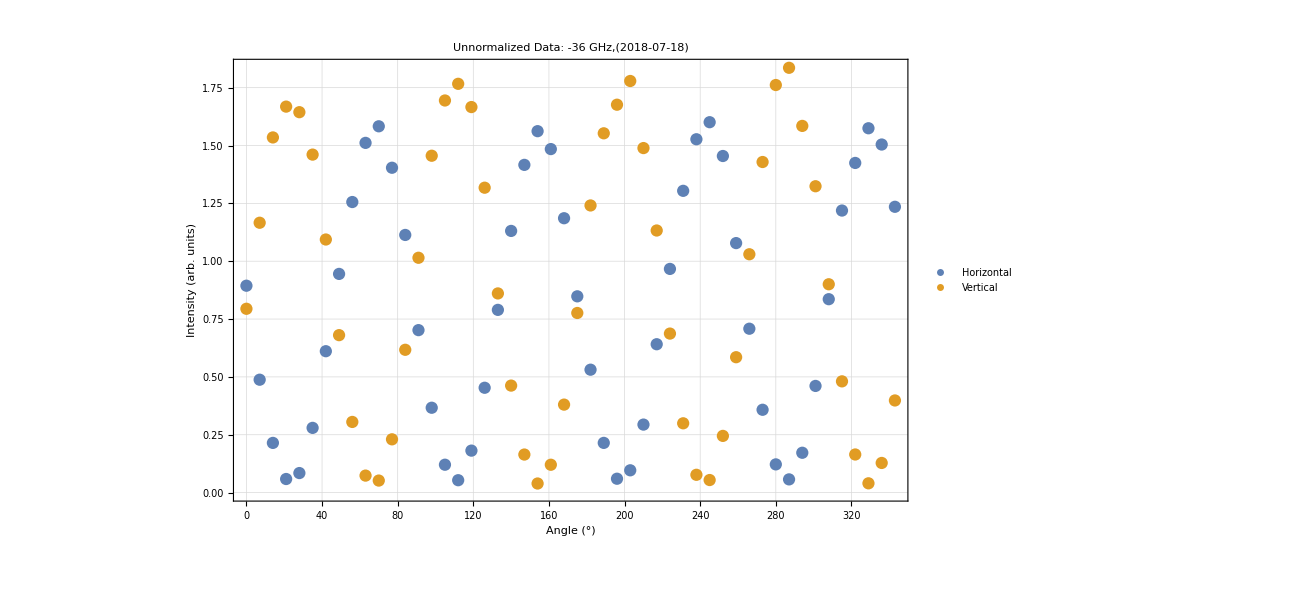

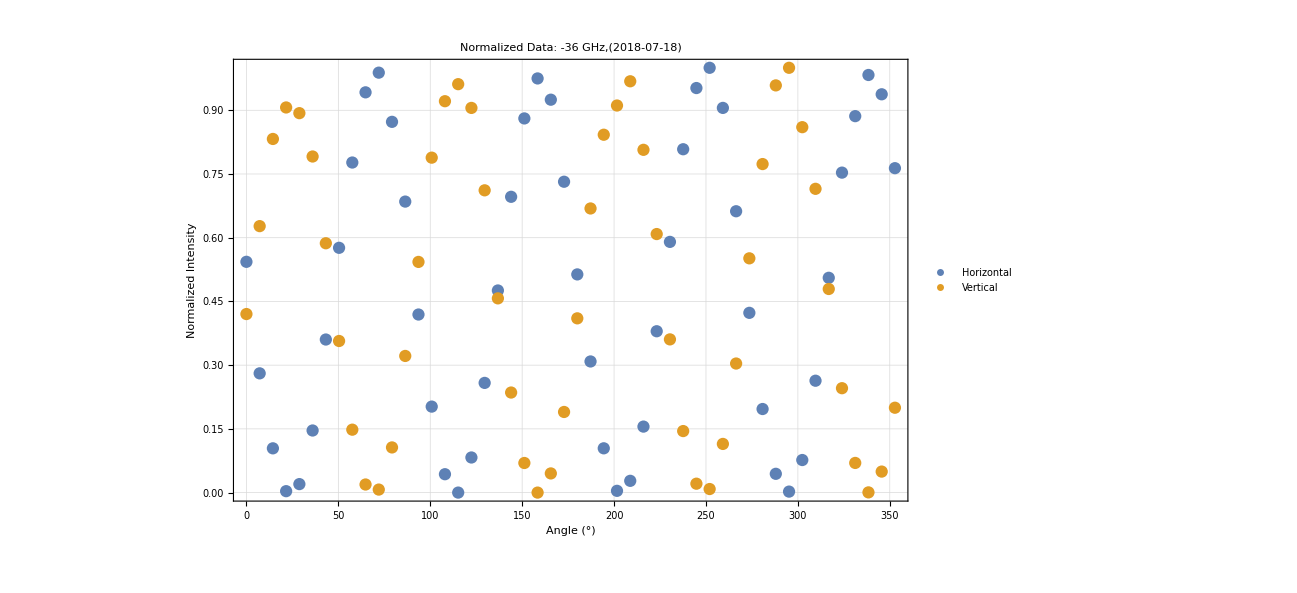

Power::infy: Infinite expression 1/0. encountered.

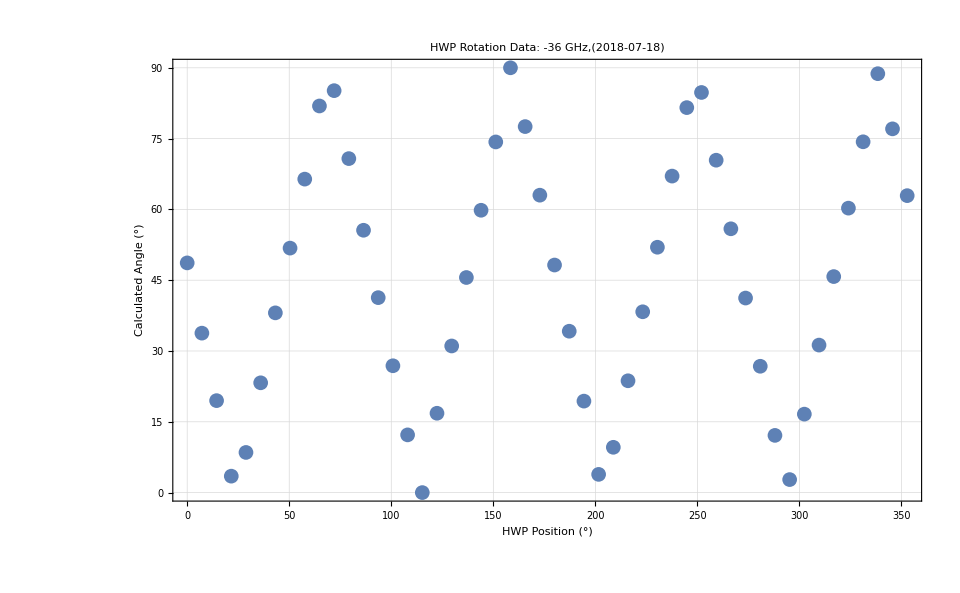

{{144/5,8.50615},{36,23.2597},{216/5,38.0796},{252/5,51.7976},{288/5,66.4143},{324/5,81.9107}}

FittedModel[-49.7576+2.02462 θ]

{0.726227,0.0150083}

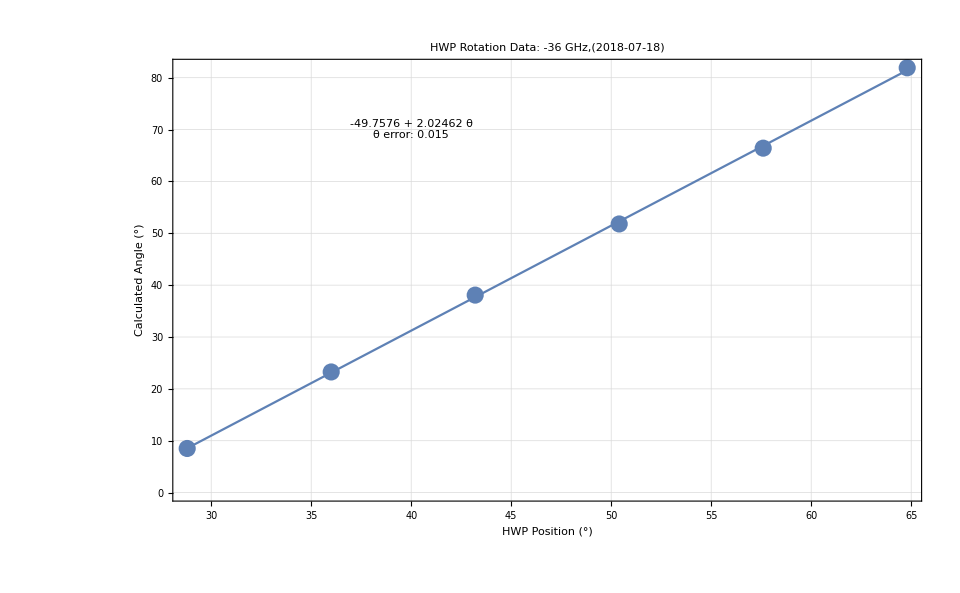

<|Slope→2.02462|>

<|Slope→2.02462,Slope Error→0.0150083|>

Dataset[<>]

{{-36.9719,-0.458261},{-36.6874,-0.267101},{-36.2605,-0.392056},{-35.7863,-0.209355},{-35.2646,-0.31785},{-34.7903,-0.199764},{-34.2686,0.429366},{-33.7469,-0.510412},{-33.1777,-0.613703},{-32.6086,-0.29455},{-32.0395,0.428232},{-31.4703,-0.236614},{-30.9012,-0.0746737},{-30.3321,-0.52461},{-29.7629,0.563697},{-29.1463,0.626486},{-28.5298,-0.460448},{-27.9132,-0.218638},{-27.2966,-0.140056},{-26.68,0.121749},{-26.0634,-0.375888},{-25.3994,-0.00497343},{-24.7828,-0.0351474},{-24.1188,-0.59227},{-23.4548,-0.228459},{-22.8382,-0.4887},{-22.1742,0.458763},{-21.5101,-0.0619875},{-20.7987,-0.574351},{-20.0872,-0.135755},{-19.3757,-0.0499112},{-18.6643,-0.0267659},{-17.9528,-0.461818},{-17.2413,-0.491392},{-16.4824,-0.0953847},{-15.7235,-0.315252},{-15.012,-0.0885171},{-14.2531,-0.484472},{-13.5416,-0.369969},{-12.7827,-0.843819},{-12.0238,-0.281103},{-11.2648,-0.746749},{-10.5059,-0.0398754},{-9.79439,-0.413055},{-9.08288,-0.170175},{-8.2765,-1.11884},{-7.51755,0.0094105},{-6.71117,-0.0565393},{-5.90478,-0.474359},{-5.14583,-1.32648},{-4.33943,-0.717694},{6.19145,0.0570583},{6.99789,0.139407},{7.80434,0.807323},{8.61079,0.341627},{9.46468,0.224494},{10.2711,-0.364904},{11.125,0.360893},{11.9315,-0.00212332},{12.738,-0.0746675},{13.5919,-0.0236887},{14.3984,0.0853666},{15.2048,0.165613},{16.0113,0.159713},{16.8652,0.133187},{17.6717,0.940336},{18.5257,0.767125},{19.3322,0.171496},{20.1861,0.568899},{20.9926,0.43221},{21.8465,0.635277},{22.6531,-0.773841},{23.507,0.104665},{24.361,0.279276},{25.1675,1.09875},{25.9266,0.130287},{26.7331,-0.230634},{27.5871,0.629346},{28.3936,0.481414},{29.2476,0.500192},{30.1016,0.387545},{31.003,0.280555},{31.857,0.317855},{32.6636,0.410423},{33.5176,0.0515029},{34.3716,1.06874},{35.1307,0.507254},{35.9847,0.0569686},{36.7913,0.436754},{37.5978,0.657008},{38.4044,-0.204625},{39.2584,0.53874},{40.1125,0.165756},{40.9665,-0.104684},{41.7256,-0.457805},{42.5797,0.348549},{43.4337,0.0544655},{44.2878,0.0164338},{45.0944,0.229171},{45.901,0.534031},{46.7551,0.0754812},{47.5617,0.597588},{52.0219,-0.0112625},{52.8759,-0.327422},{53.6826,-0.0230413}}

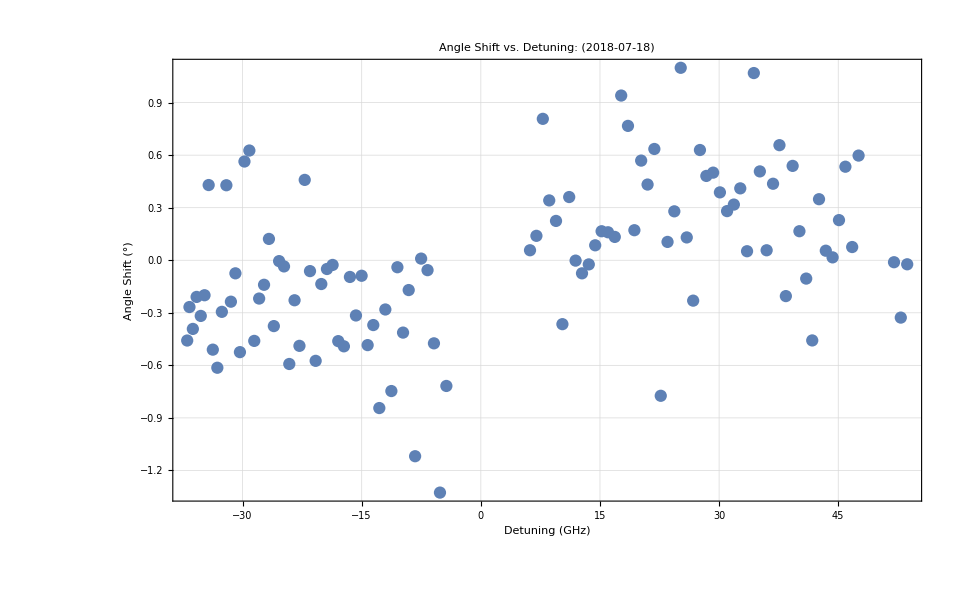

{-3.81426,6.68463}

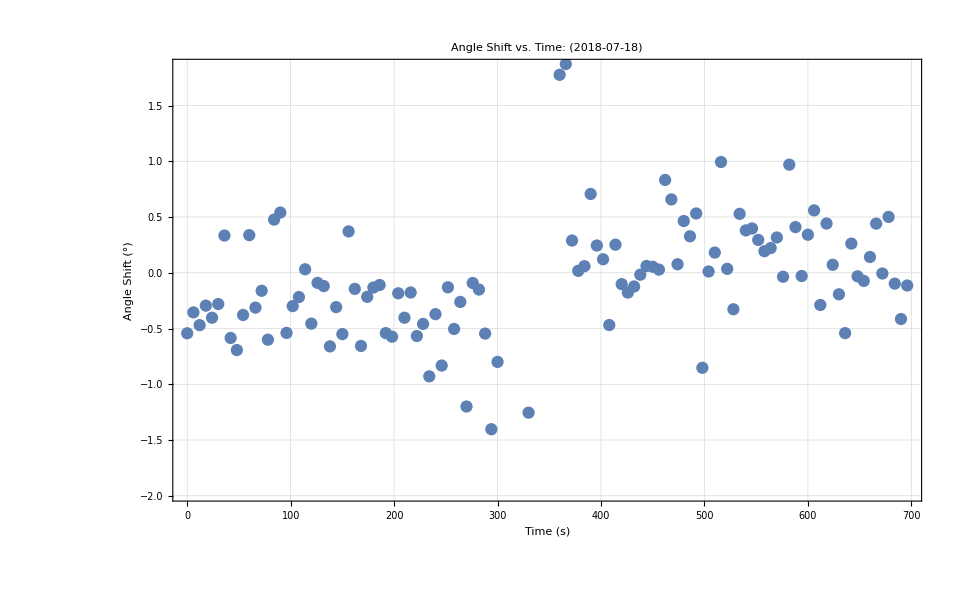

```mathematica
SetDirectory[FileNameJoin[{folder,"2018-07-10_BalancedPhotoDetectorRound2","data","magnetsOffCellWarmLaserClipped"}]];
absFiles=FileNames[StringExpression["FScan",__,"_",__,DigitCharacter,".dat"]]
rotationFiles=FileNames["FDayRotation"~~RegularExpression[".{17,17}"]~~".dat"]

results=<||>;
qualifier="farDetuned";
file=ImportFile[rotationFiles[[1]]];
rawDataset=file[[2]];
headerInfo=file[[1]];
date=StringTake[headerInfo["File"],{17,26}];
(* Graph the unnormalized Data *)
rawData=Normal[Values[rawDataset[All,{"STEP","PMP","PRB"}]]];
horizontalData=Normal[Values[rawDataset[All,{"STEP","PMP"}]]];
verticalData=Normal[Values[rawDataset[All,{"STEP","PRB"}]]];
label="Unnormalized Data";
subLabel=": -36 GHz,("<>date<>")";
plotLegends={"Horizontal","Vertical"};
frameLabels={"Angle (°)","Intensity (arb. units)"};
rawDataPlot=ListPlot[{horizontalData,verticalData},PlotLabel-> label<>subLabel,PlotLegends->plotLegends,FrameLabel->frameLabels]

(* Graph the normalized Data *)
refInt=Mean[rawDataset[All,"REF"]]; (* The reference cell intensity when the measurement was made. This is used to reduce the effects of laser intensity drift on our BPD measurements *)
minPMP=Min[rawDataset[All,"PMP"]];
maxPMP=Max[rawDataset[All,"PMP"]];
minPRB=Min[rawDataset[All,"PRB"]];
maxPRB=Max[rawDataset[All,"PRB"]];
intensityNormalizedData=rawDataset[All,{#["STEP"]*360/350&,(#["PMP"]-minPMP)/(maxPMP-minPMP)&, (#["PRB"]-minPRB)/(maxPRB-minPRB)&,ArcTan[Sqrt[((#["PMP"]-minPMP)/((maxPMP-minPMP))/(#["PRB"]-minPRB)/(maxPRB-minPRB))]]&}];
hNormData=rawDataset[All,{#["STEP"]*360/350&,(#["PMP"]-minPMP)/(maxPMP-minPMP)&}];
vNormData=rawDataset[All,{#["STEP"]*360/350&,(#["PRB"]-minPRB)/(maxPRB-minPRB)&}];
label="Normalized Data";
subLabel=": -36 GHz,("<>date<>")";
plotLegends={"Horizontal","Vertical"};
frameLabels={"Angle (°)","Normalized Intensity"};
normalizedPlot=ListPlot[{hNormData,vNormData},PlotLabel-> label<>subLabel,PlotLegends->plotLegends,FrameLabel->frameLabels]


(* Graph the angle calculation data *)
angleData={};
For[i=1,i≤Length[hNormData],i++,
AppendTo[angleData,{hNormData[[i]][[1]],Check[ArcTan[Sqrt[hNormData[[i]][[2]]/vNormData[[i]][[2]]]]*180/π,90]}];
]
label="HWP Rotation Data";
plotLegends={};
subLabel=": -36 GHz,("<>date<>")";
frameLabels={"HWP Position (°)","Calculated Angle (°)"};
ListPlot[angleData,PlotLabel-> label<>subLabel,PlotLegends->plotLegends,FrameLabel->frameLabels]

linearModelData=Take[angleData,{5,10}]
lm=LinearModelFit[linearModelData,θ,θ]
lm["ParameterErrors"]
label="HWP Rotation Data";
subLabel=": -36 GHz,("<>date<>")";
plotLegends={};
frameLabels={"HWP Position (°)","Calculated Angle (°)"};
linearPlot=ListPlot[linearModelData,PlotLabel-> label<>subLabel,PlotLegends->plotLegends,FrameLabel->frameLabels];

model=Plot[lm[θ],{θ,linearModelData[[1]][[1]],linearModelData[[-1]][[1]]}];
Show[{linearPlot,model,Graphics[Text[ToString[lm["BestFit"]]<>"\nθ error: "<> ToString[NumberForm[lm["ParameterErrors"][[2]],3]],{40,70}],BaseStyle->15]}]
AppendTo[results,"Slope"->lm["BestFitParameters"][[2]]]
AppendTo[results,"Slope Error"->lm["ParameterErrors"][[2]]]

(* Detuning Graphs *)
importedFile=ImportFile[absFiles[[1]]];
absFileHeader=importedFile[[1]];
absFileData=importedFile[[2]];
date=StringTake[headerInfo["File"],{17,26}];
absFileDataLong=Select[absFileData,#WAV>794.9872844&];
absFileDataShort=Select[absFileData,#WAV<794.9662036&];
absFileData=Join[absFileDataLong,absFileDataShort];
detData=Normal[absFileData[All,{c/100/#["WAV"]-ν0*1*^-9 &,"PMP","PRB","REF"}],]
angleData={};
For[i=1,i≤Length[detData],i++,
AppendTo[angleData,{detData[[i]][[1]],ArcTan[Sqrt[(detData[[i]][[2]]-minPMP)/(maxPMP-minPMP)/((detData[[i]][[3]]-minPRB)/(maxPRB-minPRB))]]*180/π}];
];
Transpose[angleData];
averageAngle=Mean[Transpose[angleData][[2]]];
angleShiftData=Transpose[{Transpose[angleData][[1]],Transpose[angleData][[2]]-averageAngle}]
label="Angle Shift vs. Detuning";
subLabel=": ("<>date<>")";
plotLegends={};
frameLabels={"Detuning (GHz)","Angle Shift (°)"};
shiftVsDetuningPlot=ListPlot[angleShiftData,PlotLabel-> label<>subLabel,PlotLegends->plotLegends,FrameLabel->frameLabels,PlotRange->Full]

importedFile=ImportFile[absFiles[[1]]];
absFileHeader=importedFile[[1]];
absFileData=importedFile[[2]];
detData=Normal[absFileData[All,{"VOLT","PMP","PRB"}]];
angleData={};
For[i=1,i≤Length[detData],i++,
AppendTo[angleData,{detData[[i]][[1]],ArcTan[Sqrt[(detData[[i]][[2]]*refInt/detData[[i]][[3]]-minPMP)/(maxPMP-minPMP)/((detData[[i]][[3]]*refInt/detData[[i]][[3]]-minPRB)/(maxPRB-minPRB))]]*180/π}];
];
Transpose[angleData];
averageAngle=Mean[Transpose[angleData][[2]]];
angleShiftData=Transpose[{Transpose[angleData][[1]]*6,Transpose[angleData][[2]]-averageAngle}];
mM=MinMax[Transpose[angleShiftData][[2]]]

label="Angle Shift vs. Time";
subLabel=": ("<>date<>")";
plotLegends={};
frameLabels={"Time (s)","Angle Shift (°)"};
ListPlot[angleShiftData,PlotLabel-> label<>subLabel,PlotLegends->plotLegends,FrameLabel->frameLabels]

AppendTo[results,"Detuning Angle Range"->mM[[2]]-mM[[1]]];
AppendTo[results,"Angle vs. Detuning"-> shiftVsDetuningPlot];
```

## Magnets off, cell warm, laser clipped, more sample points per measurement

{FScanBPD2018-07-18_125924.dat}

{FDayRotation2018-07-18_125730.dat,FDayRotation2018-07-18_125836.dat}

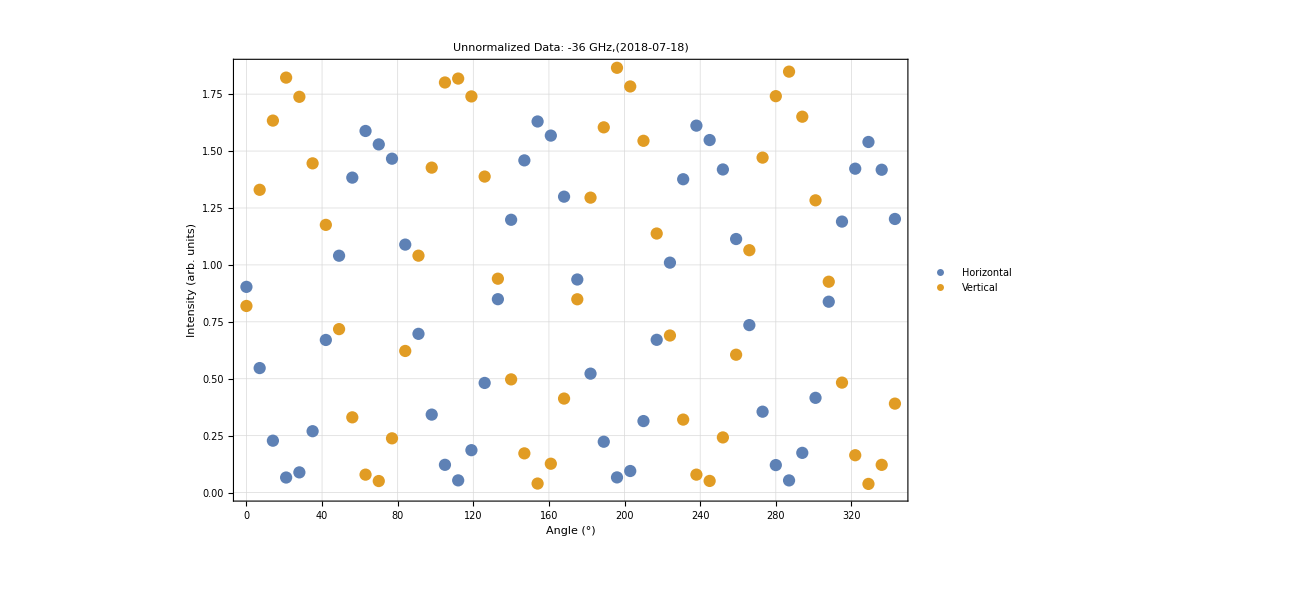

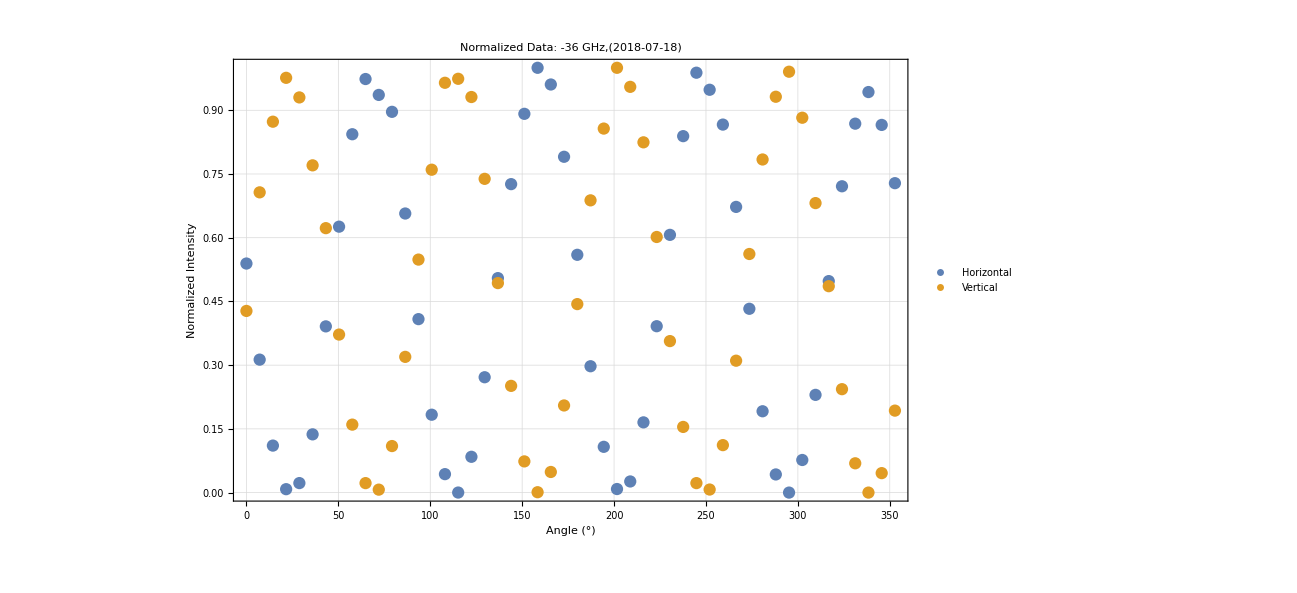

Power::infy: Infinite expression 1/0. encountered.

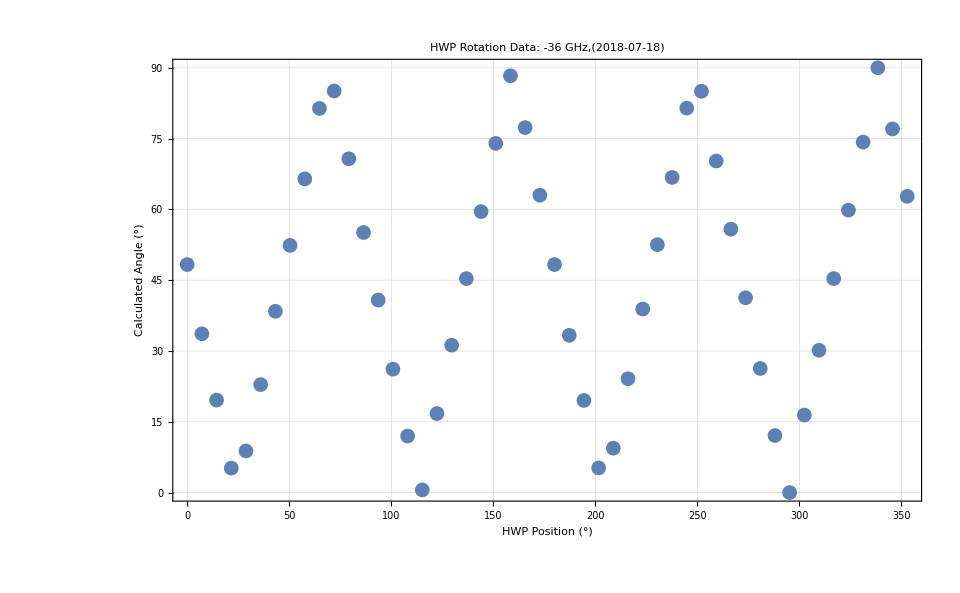

{{144/5,8.81489},{36,22.8716},{216/5,38.4081},{252/5,52.3718},{288/5,66.4664},{324/5,81.3933}}

FittedModel[-49.2217+2.01444 θ]

{0.661588,0.0136724}

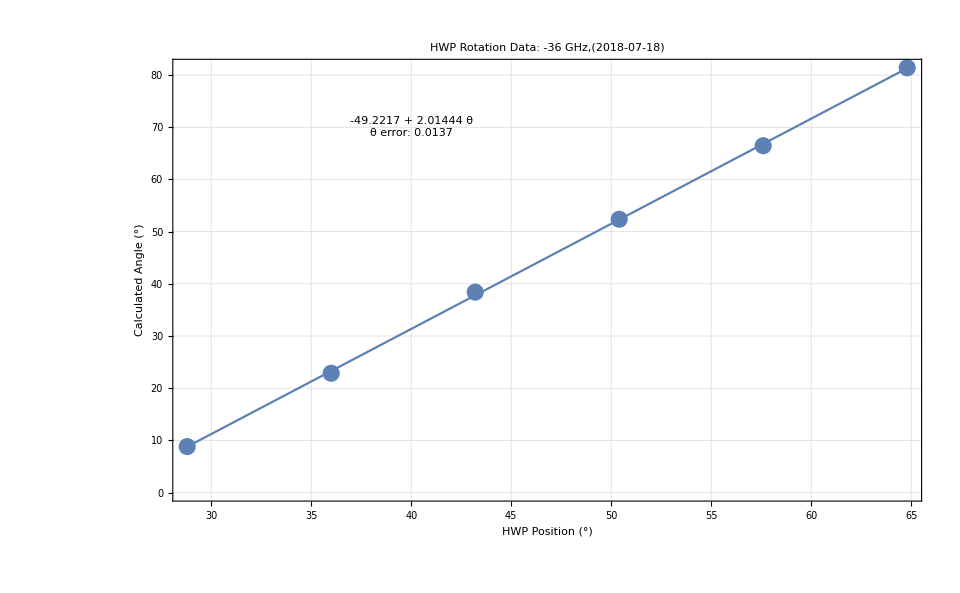

<|Slope→2.01444|>

<|Slope→2.01444,Slope Error→0.0136724|>

Dataset[<>]

{{-36.8771,-0.139498},{-36.6399,-0.309922},{-36.2605,-0.802027},{-35.7863,0.0584664},{-35.312,0.0423765},{-34.7903,-0.1837},{-34.316,-0.0398548},{-33.7943,0.237445},{-33.2252,-0.523469},{-32.7035,0.0635576},{-32.1343,0.0235227},{-31.5652,-0.42873},{-30.9961,-0.48364},{-30.4269,-0.102882},{-29.8578,-0.49135},{-29.2412,-0.50617},{-28.6246,0.337507},{-28.008,-0.0750777},{-27.3915,-0.0682901},{-26.7749,-0.624444},{-26.1109,-0.395623},{-25.4469,-0.314747},{-24.7828,-0.0819499},{-24.1188,-0.00983966},{-23.4074,0.092466},{-22.7908,-0.165908},{-22.0793,-0.111405},{-21.4153,-0.188341},{-20.7513,-0.527255},{-20.0872,-0.0147295},{-19.3757,-0.0548364},{-18.6643,-0.409006},{-18.0002,-0.0723701},{-17.2413,-0.698978},{-16.435,-0.455013},{-15.7235,-0.343074},{-14.9646,-0.541506},{-14.2057,0.053146},{-13.4467,-0.0911888},{-12.7353,-0.00157311},{-11.9763,-0.291596},{-11.2648,-0.334859},{-10.5059,-0.294377},{-9.74695,-0.47867},{-9.03544,-0.471582},{-8.2765,-0.046225},{-7.51755,0.139946},{-6.7586,-0.966688},{-5.99965,-0.285529},{-5.19326,-1.1128},{-4.33943,-1.06424},{6.14401,0.461581},{6.99789,0.668575},{7.85178,0.105793},{8.65823,-0.177909},{9.51212,-0.243119},{10.366,0.384726},{11.1725,0.105205},{11.9789,-0.0172969},{12.7854,0.076576},{13.5919,-0.620503},{14.3984,-0.960695},{15.2048,-0.261103},{16.0588,0.438425},{16.9127,0.421876},{17.7666,-0.269227},{18.6205,0.178598},{19.427,0.343817},{20.281,0.740938},{21.1349,-0.0758378},{21.9889,0.0520335},{22.8428,0.506406},{23.6493,0.470581},{24.5033,0.854578},{25.2624,-0.069513},{26.0689,0.126135},{26.8754,0.471989},{27.682,0.26545},{28.4411,0.974195},{29.295,0.657838},{30.1016,0.099721},{30.9556,-0.158652},{31.8096,0.890564},{32.6636,0.618585},{33.5176,0.0661769},{34.3716,-0.167952},{35.1781,1.73029},{36.0321,0.69693},{36.8862,0.01524},{37.6927,0.0907158},{38.5468,0.373329},{39.3533,-0.072023},{40.2074,0.829974},{40.9665,0.788677},{41.7731,0.787714},{42.6271,0.606291},{43.4337,0.0988934},{44.2403,-0.158277},{45.0944,-0.607133},{45.901,0.394203},{50.4086,0.100468},{51.2152,0.473584},{52.0219,0.636536},{52.8759,-0.10484},{53.6826,-0.0845971}}

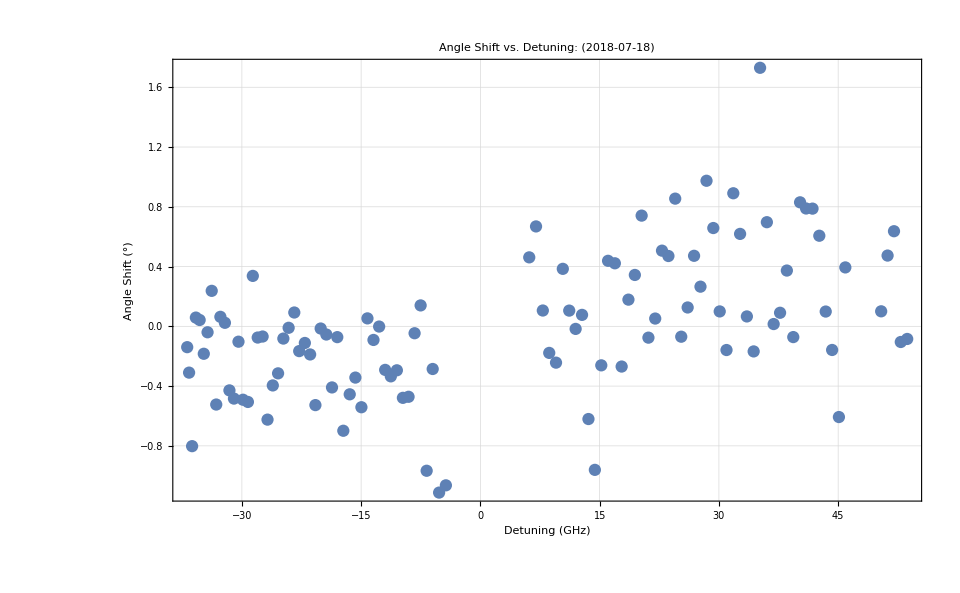

{-4.02174,4.78749}

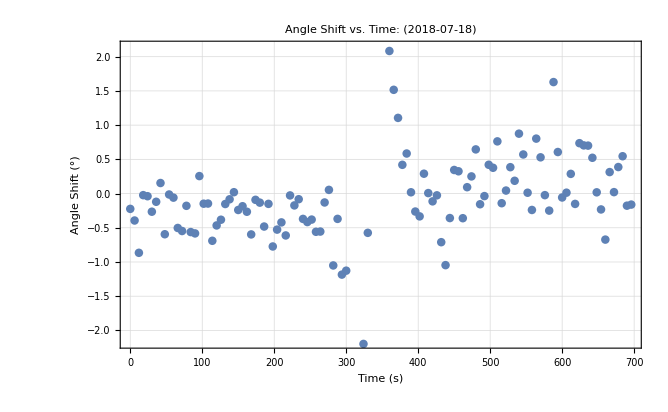

```mathematica
SetDirectory[FileNameJoin[{folder,"2018-07-10_BalancedPhotoDetectorRound2","data","magnetsOffCellWarmLaserClippedMoreSamplePoints"}]];
absFiles=FileNames[StringExpression["FScan",__,"_",__,DigitCharacter,".dat"]]
rotationFiles=FileNames["FDayRotation"~~RegularExpression[".{17,17}"]~~".dat"]

results=<||>;
qualifier="farDetuned";
file=ImportFile[rotationFiles[[1]]];
rawDataset=file[[2]];
headerInfo=file[[1]];
date=StringTake[headerInfo["File"],{17,26}];
(* Graph the unnormalized Data *)
rawData=Normal[Values[rawDataset[All,{"STEP","PMP","PRB"}]]];
horizontalData=Normal[Values[rawDataset[All,{"STEP","PMP"}]]];
verticalData=Normal[Values[rawDataset[All,{"STEP","PRB"}]]];
label="Unnormalized Data";
subLabel=": -36 GHz,("<>date<>")";
plotLegends={"Horizontal","Vertical"};
frameLabels={"Angle (°)","Intensity (arb. units)"};
rawDataPlot=ListPlot[{horizontalData,verticalData},PlotLabel-> label<>subLabel,PlotLegends->plotLegends,FrameLabel->frameLabels]

(* Graph the normalized Data *)
refInt=Mean[rawDataset[All,"REF"]]; (* The reference cell intensity when the measurement was made. This is used to reduce the effects of laser intensity drift on our BPD measurements *)
minPMP=Min[rawDataset[All,"PMP"]];
maxPMP=Max[rawDataset[All,"PMP"]];
minPRB=Min[rawDataset[All,"PRB"]];
maxPRB=Max[rawDataset[All,"PRB"]];
intensityNormalizedData=rawDataset[All,{#["STEP"]*360/350&,(#["PMP"]-minPMP)/(maxPMP-minPMP)&, (#["PRB"]-minPRB)/(maxPRB-minPRB)&,ArcTan[Sqrt[((#["PMP"]-minPMP)/((maxPMP-minPMP))/(#["PRB"]-minPRB)/(maxPRB-minPRB))]]&}];
hNormData=rawDataset[All,{#["STEP"]*360/350&,(#["PMP"]-minPMP)/(maxPMP-minPMP)&}];
vNormData=rawDataset[All,{#["STEP"]*360/350&,(#["PRB"]-minPRB)/(maxPRB-minPRB)&}];
label="Normalized Data";
subLabel=": -36 GHz,("<>date<>")";
plotLegends={"Horizontal","Vertical"};
frameLabels={"Angle (°)","Normalized Intensity"};
normalizedPlot=ListPlot[{hNormData,vNormData},PlotLabel-> label<>subLabel,PlotLegends->plotLegends,FrameLabel->frameLabels]


(* Graph the angle calculation data *)
angleData={};
For[i=1,i≤Length[hNormData],i++,
AppendTo[angleData,{hNormData[[i]][[1]],Check[ArcTan[Sqrt[hNormData[[i]][[2]]/vNormData[[i]][[2]]]]*180/π,90]}];
]
label="HWP Rotation Data";
plotLegends={};
subLabel=": -36 GHz,("<>date<>")";
frameLabels={"HWP Position (°)","Calculated Angle (°)"};
ListPlot[angleData,PlotLabel-> label<>subLabel,PlotLegends->plotLegends,FrameLabel->frameLabels]

linearModelData=Take[angleData,{5,10}]
lm=LinearModelFit[linearModelData,θ,θ]
lm["ParameterErrors"]
label="HWP Rotation Data";
subLabel=": -36 GHz,("<>date<>")";
plotLegends={};
frameLabels={"HWP Position (°)","Calculated Angle (°)"};
linearPlot=ListPlot[linearModelData,PlotLabel-> label<>subLabel,PlotLegends->plotLegends,FrameLabel->frameLabels];

model=Plot[lm[θ],{θ,linearModelData[[1]][[1]],linearModelData[[-1]][[1]]}];
Show[{linearPlot,model,Graphics[Text[ToString[lm["BestFit"]]<>"\nθ error: "<> ToString[NumberForm[lm["ParameterErrors"][[2]],3]],{40,70}],BaseStyle->15]}]
AppendTo[results,"Slope"->lm["BestFitParameters"][[2]]]
AppendTo[results,"Slope Error"->lm["ParameterErrors"][[2]]]

(* Detuning Graphs *)
importedFile=ImportFile[absFiles[[1]]];
absFileHeader=importedFile[[1]];
absFileData=importedFile[[2]];
date=StringTake[headerInfo["File"],{17,26}];
absFileDataLong=Select[absFileData,#WAV>794.9872844&];
absFileDataShort=Select[absFileData,#WAV<794.9662036&];
absFileData=Join[absFileDataLong,absFileDataShort];
detData=Normal[absFileData[All,{c/100/#["WAV"]-ν0*1*^-9 &,"PMP","PRB","REF"}],]
angleData={};
For[i=1,i≤Length[detData],i++,
AppendTo[angleData,{detData[[i]][[1]],ArcTan[Sqrt[(detData[[i]][[2]]-minPMP)/(maxPMP-minPMP)/((detData[[i]][[3]]-minPRB)/(maxPRB-minPRB))]]*180/π}];
];
Transpose[angleData];
averageAngle=Mean[Transpose[angleData][[2]]];
angleShiftData=Transpose[{Transpose[angleData][[1]],Transpose[angleData][[2]]-averageAngle}]
label="Angle Shift vs. Detuning";
subLabel=": ("<>date<>")";
plotLegends={};
frameLabels={"Detuning (GHz)","Angle Shift (°)"};
shiftVsDetuningPlot=ListPlot[angleShiftData,PlotLabel-> label<>subLabel,PlotLegends->plotLegends,FrameLabel->frameLabels,PlotRange->Full]

importedFile=ImportFile[absFiles[[1]]];
absFileHeader=importedFile[[1]];
absFileData=importedFile[[2]];
detData=Normal[absFileData[All,{"VOLT","PMP","PRB"}]];
angleData={};
For[i=1,i≤Length[detData],i++,
AppendTo[angleData,{detData[[i]][[1]],ArcTan[Sqrt[(detData[[i]][[2]]*refInt/detData[[i]][[3]]-minPMP)/(maxPMP-minPMP)/((detData[[i]][[3]]*refInt/detData[[i]][[3]]-minPRB)/(maxPRB-minPRB))]]*180/π}];
];
Transpose[angleData];
averageAngle=Mean[Transpose[angleData][[2]]];
angleShiftData=Transpose[{Transpose[angleData][[1]]*6,Transpose[angleData][[2]]-averageAngle}];
mM=MinMax[Transpose[angleShiftData][[2]]]

label="Angle Shift vs. Time";
subLabel=": ("<>date<>")";
plotLegends={};
frameLabels={"Time (s)","Angle Shift (°)"};
ListPlot[angleShiftData,PlotLabel-> label<>subLabel,PlotLegends->plotLegends,FrameLabel->frameLabels]

AppendTo[results,"Detuning Angle Range"->mM[[2]]-mM[[1]]];
AppendTo[results,"Angle vs. Detuning"-> shiftVsDetuningPlot];
```

## Analyze the Data

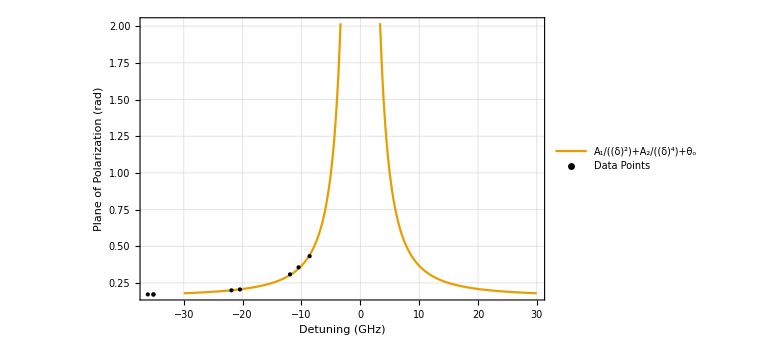
{<|n1pt→-1191.68,measuredTheta_0→8.86,calcTheta_0→0.156098,n_rbplot→-Graphics-,n_rbdataset→{{-35.1597,0.170754},{-36.1149,0.171841},{-35.1597,0.171898},{-21.901,0.19952},{-20.4539,0.205512},{-11.9422,0.308307},{-10.495,0.356381},{-8.61281,0.43238}},p_rb→0.0158312,46,WavemeterOffset(GHz)→0,Revolutions→1,DataPointsPerRev→50,NumVolts→18,StepSize→7|>,82,<|1|>}
 |  |  |  |

Dataset[<>]

```mathematica
database=entries;
Dataset[database][All,{"p_rb","n_rb","time","CVGauge(N2)(Torr)","SetTemp(Res)","PumpLaserTACurrent(mA)","Comments"}]
```

### Polarization of Rubidium vs. Power

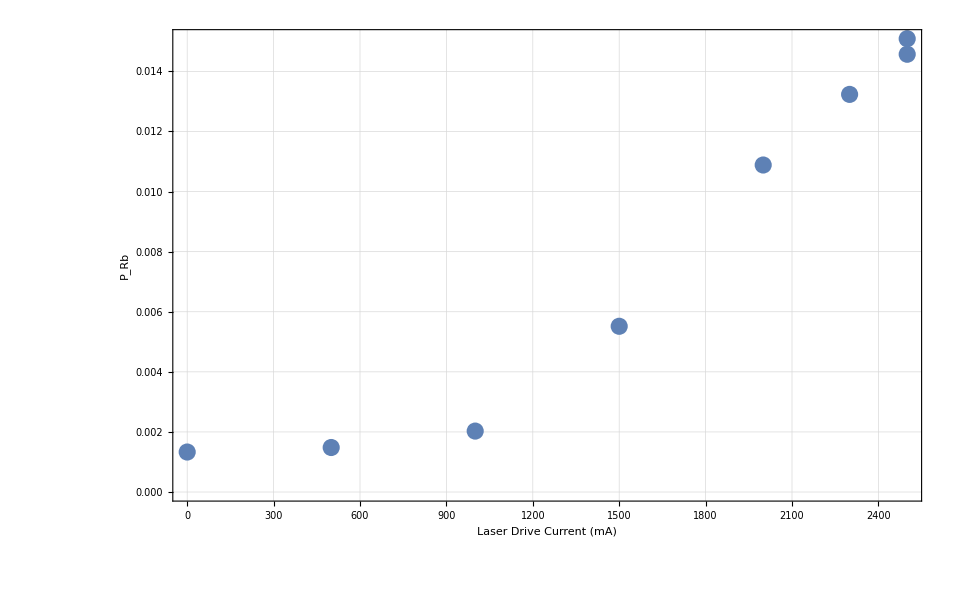

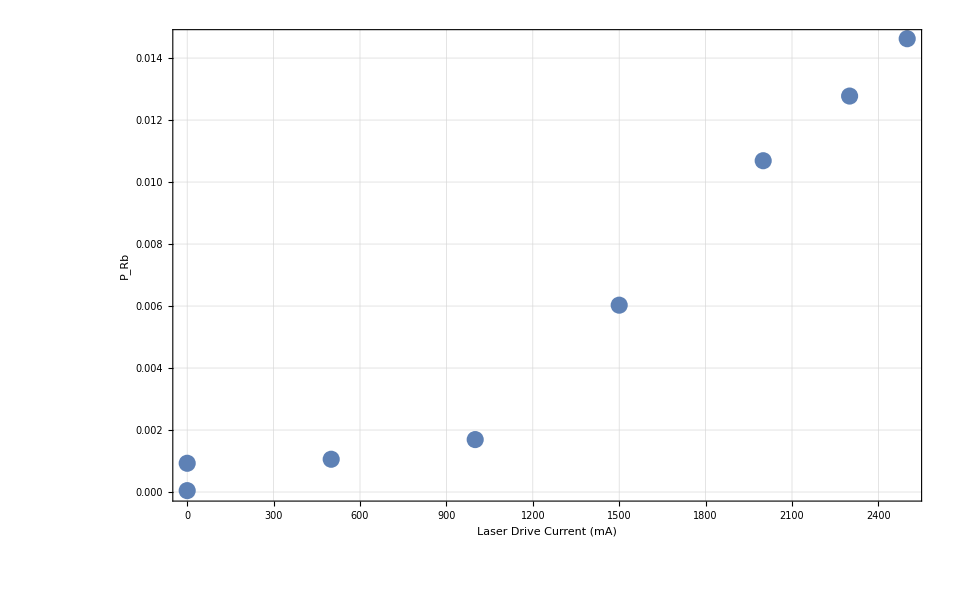

```mathematica
ds=Dataset[database];
ListPlot[ds[Select[#time<DateObject["22 Apr. 2018 1:30:30 am"]&]][All,{"PumpLaserTACurrent(mA)","p_rbs+"}],Frame->True,FrameLabel->{"Laser Drive Current (mA)","P_Rb"}]
ListPlot[ds[Select[#time>DateObject["22 Apr. 2018 1:30:30 am"]&&#time<DateObject["22 Apr. 2018 10 am"]&]][All,{#["PumpLaserTACurrent(mA)"],#["p_rbs+"]}&],Frame->True,FrameLabel->{"Laser Drive Current (mA)","P_Rb"},GridLines->{Automatic,Automatic}]
```

### Laser Power Analysis

{Microamperes,Microamperes,Microamperes}

FittedModel[-94.2161+0.0788145 x]

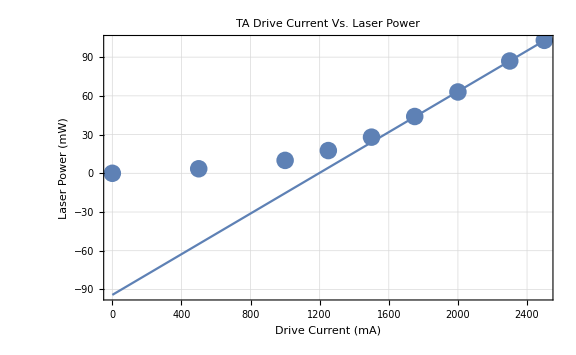

```mathematica
drive=QuantityArray[{0,500,1000,1250,1500,1750,2000,2300,2500},"mAmperes"];
power=QuantityArray[{0.,3.5,10.0,17.6,28,44,63,87,103},"mWatts"];
pdCurrent=QuantityArray[{0,2.60,4.25},"microAmperes"];
QuantityUnit[pdCurrent]

lmFit=LinearModelFit[Take[Transpose[{QuantityMagnitude[drive],QuantityMagnitude[power]}],{6,-1}],x,x]
Show[{Plot[lmFit[x],{x,0,2500}],ListPlot[Transpose[{drive,power}],PlotMarkers->{Automatic,18}]},PlotLabel-> "TA Drive Current Vs. Laser Power",FrameLabel-> {"Drive Current (mA)","Laser Power (mW)"}]
```

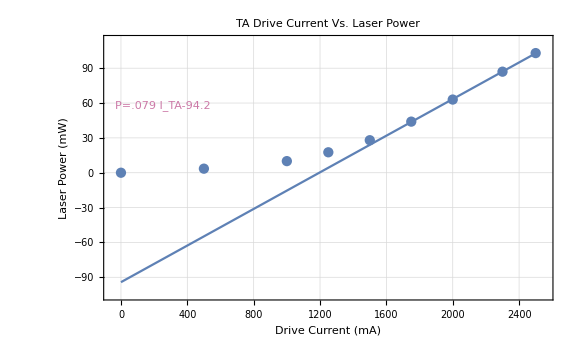

## Comparing Functional Form Models

```mathematica
(* We have a couple functional models that are very similar in form, and I just want to be sure that they give equivalent results with the same dataset. 

 -Wu is from the 1986 paper from the author with the same name.
 -Litaker comes from his thesis, it's esentially a re-derivation of Wu. 
-Ahrendsen comes from my own derivation of Wu, containing another frequency term that I believe Litaker should be including to be equivalent to Wu. I obtained my formula by converting Wu's to use frequency instead of wavelength.
*)
```

## Functions for converting different ways of measuring

```mathematica
(*Functions for converting ways of measuring laser color*)
δ2ν[δ_]:=δ+ν0*1*^-9;
ν2λ[ν_]:=c*.01/ν;
λ2Δλ[λ_]:=λ-(λ0*1*^7);
δ2Δλ[δ_]:=λ2Δλ[ν2λ[δ2ν[δ]]];
(*Functions for converting ways of measuring amount of rotation *)
deg2rad[deg_]:=deg/180*π;
rad2deg[rad_]:=rad/π*180;
convertδdataset2Δλ[dataset_]:=Transpose[{δ2Δλ[Transpose[dataset][[1]]],Transpose[dataset][[2]]}];
convertGHzDataset2Hz[dataset_]:=Transpose[{1*^9*Transpose[dataset][[1]],Transpose[dataset][[2]]}];
convert°dataset2rad[dataset_]:=Transpose[{Transpose[dataset][[1]],deg2rad[Transpose[dataset][[2]]]}];
```